# Stiffness-dependent tissue wetting enables optimal collective cell durotaxis

## Function definitions and parameters

- x0: center-of-mass position [µm]
- L0: contact radius of the basal monolayer (R in the text) [µm]
- Lc: nematic length [µm]
- R: radius of the spherical cap modelling the cluster (R_sphere in the text) [µm]
- H: height of the cluster [µm]
- Esubstrate: stiffness of the substrate (linear with position on the gel) [kPa]
- ζi: active traction parameter (either linear ζilinear or saturated ζisat with stiffness) [kPa/µm]
- ξ: friction parameter (either linear ξlinear or saturated ξsat with stiffness) [kPa·s/µm^2]
- P: pressure of the clusters on top of the gel (either linear Plinear or saturated Psat with stiffness) [kPa]

```mathematica
(* To draw ticks in the plots *) 
s[j_] := Table[{j i, j i, {0, 0.01}}, {i, -100, 100}];
p[j_] := Table[{j i/2, "", {0, 0.01}}, {i, -99, 99}];
ticks[j_] := ArrayFlatten[{{s[j]}, {p[j]}}];
```

### Substrate stiffness, active traction, friction, pressure, volume, height and contact angle

```mathematica
(* Substrate stiffness, active traction, friction and pressure *)
Clear[Esubstrate,ζilinear,ξlinear,Plinear,ζisat,ξsat,Psat];
Esubstrate[x_,x0idef_,E0_,Egrad_]:=E0+Egrad*(x-x0idef);     
ζilinear[x_,x0idef_,ζi0def_,ζigrad_]:=ζi0def+ζigrad*(x-x0idef);
ξlinear[x_,x0idef_,ξ0def_,ξgrad_]:=ξ0def+ξgrad*(x-x0idef);
Plinear[x_,x0idef_,P0def_,Pgrad_]:=P0def+Pgrad*(x-x0idef);
ζisat[Esub_,a_,Estar_]:= a*Esub/(Esub+Estar); 
ξsat[Esub_,a2_,Estar2_,ξ0def_]:=a2*Esub/(Esub+Estar2)+ξ0def; 
Psat[Esub_,aP_,EstarP_]:=aP*Esub/(Esub+EstarP);
```

Fits with experimental data just to have an idea of the order of magnitude of the parameters we are dealing with. We change their values afterwards to explore a 
broader range of model parameters:

```mathematica
(* E(x) in the gel *) 
x0idef = 0;  (* Position of the softest part of the gel E(x0idef) = E0, usually defined to 0 *) 
E0 = 0.5;
xmax = 3000; (* ~30.6*200/2.05 looking at length in Fig. 2a *) 
Emax = 100;
Egrad = (Emax-E0)/(xmax-x0idef);
Print["E0 = ", E0, " kPa, E' = ", Egrad, " kPa/µm"];
```

E0 = 0.5 kPa, E' = 0.0331667 kPa/µm

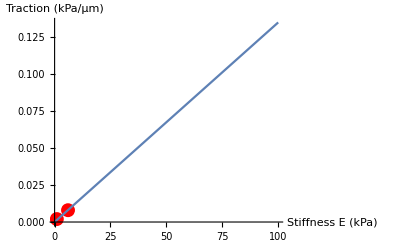

ζilinear(Esub) = 0.00135135 Esub

ζilinear(x) = 0.000675676+0.0000448198 x

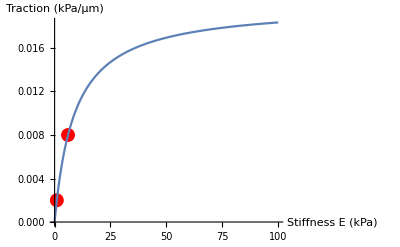

ζisat(E) = (0.02 Esub)/(9.+Esub)

Maximum ζi (linear) at Emax = 100.  kPa is 0.135135 kPa/µm: T max = 0.675676 kPa

Maximum ζi (saturated) at Emax = 100.  kPa is 0.0183486 kPa/µm: T max = 0.0917431 kPa

```mathematica
(* TRACTIONS X-Y *) 
h = 5;   (* Contact monolayer height, from Pérez-González & Ricard Alert Nat Phys 2019 *)
datatrac = {{1,0.01/h},{6,0.04/h}};   (* Approximate values of traction in Fig. 1i, in kPa (Table 2 Methods) *) 

(* Linear fit ζilinear(E)= β*E *)
line = Fit[datatrac, {Esub}, Esub];
α = CoefficientList[line,Esub][[2]];
Show[ListPlot[datatrac,PlotStyle->{Red,PointSize->0.025}],
Plot[line,{Esub,0,Emax}],AxesLabel->{"Stiffness E (kPa)","Traction (kPa/µm)"},PlotRange->{{0,Emax},Automatic}]
ζi0def = α*(E0-Egrad*x0idef);   (* ζi = α*(E0 + Egrad*(x-x0idef)) = α*(E0-Egrad*x0idef) + α*Egrad*x *) 
ζigrad = α*Egrad;
Print["ζilinear(Esub) = ", α*Esub];
Print["ζilinear(x) = ", ζilinear[x,x0idef,ζi0def,ζigrad]];

(* Saturated fit *) 
Clear[a,Estar];
sol=FindFit[datatrac,ζisat[Esub,a,Estar],{a,Estar},Esub];
a=sol[[1,2]];
Estar=sol[[2,2]];
Show[ListPlot[datatrac,PlotStyle->{Red,PointSize->0.025}],
Plot[ζisat[Esub,a,Estar],{Esub,0,Emax},PlotRange->All],PlotRange->{{0,Emax},Automatic}, AxesLabel->{"Stiffness E (kPa)","Traction (kPa/µm)"}]
Print["ζisat(E) = ", ζisat[Esub,a,Estar]];

Print["Maximum ζi (linear) at Emax = ", Esubstrate[xmax,x0idef,E0,Egrad]" kPa is ", ζilinear[xmax,x0idef,ζi0def,ζigrad], " kPa/µm: T max = ",  ζilinear[xmax,x0idef,ζi0def,ζigrad]*h, " kPa"];
Print["Maximum ζi (saturated) at Emax = ", Esubstrate[xmax,x0idef,E0,Egrad]" kPa is ", ζisat[Esubstrate[xmax,x0idef,E0,Egrad],a,Estar], " kPa/µm: T max = ",  ζisat[Esubstrate[xmax,x0idef,E0,Egrad],a,Estar]*h, " kPa"];
```

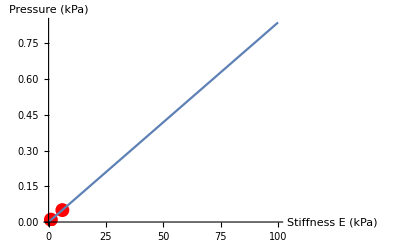

Plinear(Esub) = 0.00837838 Esub

Plinear(x) = 0.00418919+0.000277883 x

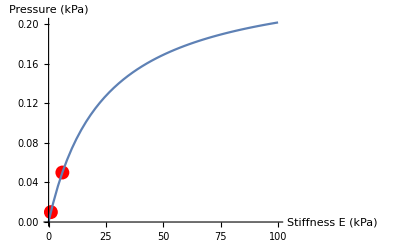

Psat(E) = (0.25 Esub)/(24.+Esub)

Maximum P (linear) at Emax = 100.  kPa is 0.837838 kPa

Maximum P (saturated) at Emax = 100.  kPa is 0.201613 kPa

```mathematica
(* PRESSURES ~ TRACTIONS Z *) 
datapress={{1,0.01},{6,0.05}};   (* Approximate values of traction in Fig. 1j, in kPa (Table 2 Methods) *) 

(* Linear fit *) 
line = Fit[datapress, {Esub}, Esub];  
α = CoefficientList[line,Esub][[2]];
Show[ListPlot[datapress,PlotStyle->{Red,PointSize->0.025}],Plot[line,{Esub,0,Emax}],AxesLabel->{"Stiffness E (kPa)","Pressure (kPa)"},PlotRange->{{0,Emax},Automatic}]
P0def = α*(E0-Egrad*x0idef);  (* P = α*(E0 + Egrad*(x-x0idef)) = α*(E0-Egrad*x0idef) + α*Egrad*x *) 
Pgrad = α*Egrad;
Print["Plinear(Esub) = ", α*Esub];
Print["Plinear(x) = ", Plinear[x,x0idef,P0def,Pgrad]];

(* Saturated fit *) 
Clear[aP,EstarP];
sol=FindFit[datapress,Psat[Esub,aP,EstarP],{aP,EstarP},Esub];
aP=sol[[1,2]];
EstarP=sol[[2,2]];
Show[ListPlot[datapress,PlotStyle->{Red,PointSize->0.025}],
Plot[Psat[Esub,aP,EstarP],{Esub,0,Emax},PlotRange->All],PlotRange->{{0,Emax},Automatic}, AxesLabel->{"Stiffness E (kPa)","Pressure (kPa)"}]
Print["Psat(E) = ", Psat[Esub,aP,EstarP]];

Print["Maximum P (linear) at Emax = ", Esubstrate[xmax,x0idef,E0,Egrad]" kPa is ", Plinear[xmax,x0idef,P0def,Pgrad], " kPa"];
Print["Maximum P (saturated) at Emax = ", Esubstrate[xmax,x0idef,E0,Egrad]" kPa is ", Psat[Esubstrate[xmax,x0idef,E0,Egrad],aP,EstarP], " kPa"];
```

```mathematica
(* Volume and height of clusters as functions of different parameters *) 
VolumeCluster[L0_,H_]:=π*H/6*(H^2+3*L0^2);  (* = VolumeCluster2[R_,H_]:=π*H^2/3*(3*R-H); *)
VolumeDewet[R_,L0_]:=π/3*(2*R^2-L0^2+2*R*Sqrt[R^2-L0^2])*(2*R-Sqrt[R^2-L0^2]);  (* The measured projected radius equals the radius of the sphere: Rproj = R *) 
HeightDewet[R_,L0_]:=R+Sqrt[R^2-L0^2]; 
VolumeWet[R_,L0_]:=π/3*(2*R^2-L0^2-2*R*Sqrt[R^2-L0^2])*(2*R+Sqrt[R^2-L0^2]);    (* The measured projected radius equals the contact radius: Rproj = L0 *) 
HeightWet[R_,L0_]:=R-Sqrt[R^2-L0^2]; 

(* Estimation of the height H through experimental data: "2021_07_15_quantification_wetting_contact_angle.xlsx" *) 
θ[x_]:=-17.84*Log[Esubstrate[x,x0idef,E0,Egrad]]+144.41;
```

### Polarity, velocity, stress and traction

```mathematica
(* Polarity field *) 
Clear[p,x0,L0,Lc,x]; 
p[x_,x0_,L0_,Lc_] = FullSimplify[DSolveValue[{Lc^2*p''[x]-p[x]==0,p[x0-L0]==-1,p[x0+L0]==1}, p[x],x]];

Manipulate[Plot[{p[x,x0,L0,Lc]},{x,x0-L0,x0+L0}, PlotRange->{{x0-L0-10,x0+L0+10},{-1.3,1.3}}, 
AxesLabel->{"Position x (µm)", "Polarity px"}],
{x0,0,100,25},{L0,100,400,50},{Lc,5,25,5}]
```

We have analytical solutions in the case with constant cell-substrate parameters (ξ, ζi constant) as well as for a linear profile of traction (ζi(x)) but constant friction (ξ):

```mathematica
(* Velocity field, λ = Sqrt[2*η/ξ] hydrodynamic lengthscale *) 
Clear[L0,Lc,ζi0,ζ,γ,λ,x,x0,η,P,R,H,h];
Clear[v1,v2];

(* Constant cell-substrate parameters (monostiffness gel) *) 
v1[x_,L0_,Lc_,ζi0_,ζ_,λ_,η_,P_,R_,h_]:=λ/(2*η)*((ζ+P*R/(2*h)*Sqrt[1-(L0/R)^2]+λ^2*Lc*ζi0*Coth[L0/Lc]/(λ^2-Lc^2)-2*ζ*λ^2/(4*λ^2-Lc^2)*(2+Csch[L0/Lc]^2))*Sinh[x/λ]/Cosh[L0/λ]+λ*Lc/Sinh[L0/Lc]*(ζ*Sinh[2*x/Lc]/((4*λ^2-Lc^2)*Sinh[L0/Lc])-ζi0*Lc*Sinh[x/Lc]/(λ^2-Lc^2)));
v2[x_,L0_,Lc_,ζi0_,ζ_,λ_,η_,P_,R_,h_]:=λ/(2*η)*((ζ+P*R/(2*Min[L0,h])*Sqrt[1-(L0/R)^2]+λ^2*Lc*ζi0*Coth[L0/Lc]/(λ^2-Lc^2)-2*ζ*λ^2/(4*λ^2-Lc^2)*(2+Csch[L0/Lc]^2))*Sinh[x/λ]/Cosh[L0/λ]+λ*Lc/Sinh[L0/Lc]*(ζ*Sinh[2*x/Lc]/((4*λ^2-Lc^2)*Sinh[L0/Lc])-ζi0*Lc*Sinh[x/Lc]/(λ^2-Lc^2))); 

(* Spreading velocity of monostiffness substrate vs L0 *)
L0max = 200;
Manipulate[
Show[{
Plot[{3600*v2[L0,L0,Lc,ζi0,ζ,Sqrt[2*η/ξ0],η,P,(H^2+L0^2)/(2*H),h]},{L0,0.0001,H},
PlotRange->{{0,L0max},All},PlotLegends->{"Dewet H>L0"},PlotStyle->{Blue},
PlotLabel->Style["γ/Min[L0,h] (fixed height H)",12,Black],
AxesLabel->{Style["Contact radius L0 (µm)",12,Black], Style["Velocity (µm/h)",12,Black]},ImageSize->Large], 
Plot[{3600*v2[L0,L0,Lc,ζi0,ζ,Sqrt[2*η/ξ0],η,-P,(H^2+L0^2)/(2*H),h]},{L0,H,L0max},
PlotRange->{{0,L0max},All},PlotLegends->{"Wet H<L0"},PlotStyle->{Blue,Dashed}], 
ParametricPlot[{{H,y}},{y,-10,10},PlotStyle->{Gray,Dashed}]}],
{Lc,15},{ζi0,0.0001,0.5},{ζ,0,-10},{η,20000},{ξ0,0.001,2},{P,0,0.1},{H,1,100},{h,5}]
```

```mathematica
(* Gradient traction with stiffness but constant friction *) 
Clear[L0,Lc,ζi0,ζ,γ,λ,x,x0,η,P,R,H,h,x0idef,ζi0def,ζigrad];
Clear[C1,C2,vEgradfun,vEgrad,C1γP,C2γP,vEgradfunγP,vEgradγP];

(* In terms of P *) 
C1[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,P_,R_,h_]:=-λ*Exp[-x0/λ]/(4*η*Cosh[L0/λ])*(-(ζ+P*R/(2*Min[L0,h])*Sqrt[1-(L0/R)^2])+λ^2*Lc*(2*ζ/(Lc*(4*λ^2-Lc^2))*(1+Coth[L0/Lc]^2)-(ζi0def+ζigrad*(x0-x0idef))/(λ^2-Lc^2)*Coth[L0/Lc]+ζigrad*Coth[L0/λ]/(λ^2-Lc^2)*(2*λ^2*Lc/(λ^2-Lc^2)-Lc-L0*Coth[L0/Lc])));
C2[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,P_,R_,h_]:=λ*Exp[x0/λ]/(4*η*Cosh[L0/λ])*(-(ζ+P*R/(2*Min[L0,h])*Sqrt[1-(L0/R)^2])+λ^2*Lc*(2*ζ/(Lc*(4*λ^2-Lc^2))*(1+Coth[L0/Lc]^2)-(ζi0def+ζigrad*(x0-x0idef))/(λ^2-Lc^2)*Coth[L0/Lc]+ζigrad*Coth[L0/λ]/(λ^2-Lc^2)*(2*λ^2*Lc/(λ^2-Lc^2)-Lc-L0*Coth[L0/Lc])))-λ^3*Lc*Exp[x0/λ]*ζigrad/(2*η*Sinh[L0/λ]*(λ^2-Lc^2))*(2*λ^2*Lc/(λ^2-Lc^2)-Lc-L0*Coth[L0/Lc]);
vEgradfun[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,P_,R_,h_]:=λ^2*Lc/(2*η*Sinh[L0/Lc])*(ζ/Sinh[L0/Lc]/(4*λ^2-Lc^2)*Sinh[2*(x-x0)/Lc]-(ζi0def+ζigrad*(x-x0idef))*Lc/(λ^2-Lc^2)*Sinh[(x-x0)/Lc]+2*ζigrad*λ^2*Lc^2/((λ+Lc)^2*(λ-Lc)^2)*Cosh[(x-x0)/Lc])+C1[x,x0,x0idef,L0,Lc,ζi0def,ζigrad,ζ,η,λ,P,R,h]*Exp[x/λ]+C2[x,x0,x0idef,L0,Lc,ζi0def,ζigrad,ζ,η,λ,P,R,h]*Exp[-x/λ];
vEgrad[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,P_,R_,h_]=vEgradfun[x,x0,x0idef,L0,Lc,ζi0def,ζigrad,ζ,η,λ,P,R,h];

(* In terms of γ *) 
C1γP[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,γP_,R_,h_]:=-λ*Exp[-x0/λ]/(4*η*Cosh[L0/λ])*(-(ζ+γP/Min[L0,h]*Sqrt[1-(L0/R)^2])+λ^2*Lc*(2*ζ/(Lc*(4*λ^2-Lc^2))*(1+Coth[L0/Lc]^2)-(ζi0def+ζigrad*(x0-x0idef))/(λ^2-Lc^2)*Coth[L0/Lc]+ζigrad*Coth[L0/λ]/(λ^2-Lc^2)*(2*λ^2*Lc/(λ^2-Lc^2)-Lc-L0*Coth[L0/Lc])));
C2γP[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,γP_,R_,h_]:=λ*Exp[x0/λ]/(4*η*Cosh[L0/λ])*(-(ζ+γP/Min[L0,h]*Sqrt[1-(L0/R)^2])+λ^2*Lc*(2*ζ/(Lc*(4*λ^2-Lc^2))*(1+Coth[L0/Lc]^2)-(ζi0def+ζigrad*(x0-x0idef))/(λ^2-Lc^2)*Coth[L0/Lc]+ζigrad*Coth[L0/λ]/(λ^2-Lc^2)*(2*λ^2*Lc/(λ^2-Lc^2)-Lc-L0*Coth[L0/Lc])))-λ^3*Lc*Exp[x0/λ]*ζigrad/(2*η*Sinh[L0/λ]*(λ^2-Lc^2))*(2*λ^2*Lc/(λ^2-Lc^2)-Lc-L0*Coth[L0/Lc]);
vEgradfunγP[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,γP_,R_,h_]:=λ^2*Lc/(2*η*Sinh[L0/Lc])*(ζ/Sinh[L0/Lc]/(4*λ^2-Lc^2)*Sinh[2*(x-x0)/Lc]-(ζi0def+ζigrad*(x-x0idef))*Lc/(λ^2-Lc^2)*Sinh[(x-x0)/Lc]+2*ζigrad*λ^2*Lc^2/((λ+Lc)^2*(λ-Lc)^2)*Cosh[(x-x0)/Lc])+C1γP[x,x0,x0idef,L0,Lc,ζi0def,ζigrad,ζ,η,λ,γP,R,h]*Exp[x/λ]+C2γP[x,x0,x0idef,L0,Lc,ζi0def,ζigrad,ζ,η,λ,γP,R,h]*Exp[-x/λ];
vEgradγP[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,γP_,R_,h_]=vEgradfunγP[x,x0,x0idef,L0,Lc,ζi0def,ζigrad,ζ,η,λ,γP,R,h]; 

(* vCM and vS gradient stiffness *) 
L0max = 200;
Manipulate[
Show[{
Plot[{3600*(vEgradγP[x0+L0,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,Plinear[x0,x0idef,P0def,Pgrad]*(H^2+L0^2)/(2*H)/2,(H^2+L0^2)/(2*H),h]+vEgradγP[x0-L0,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,Plinear[x0,x0idef,P0def,Pgrad]*(H^2+L0^2)/(2*H)/2,(H^2+L0^2)/(2*H),h])/2,
3600*(vEgradγP[x0+L0,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,Plinear[x0,x0idef,P0def,Pgrad]*(H^2+L0^2)/(2*H)/2,(H^2+L0^2)/(2*H),h]-vEgradγP[x0-L0,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,Plinear[x0,x0idef,P0def,Pgrad]*(H^2+L0^2)/(2*H)/2,(H^2+L0^2)/(2*H),h])/2},{L0,0.001,H},
PlotLegends->{"vcM dewet", "vS dewet"},PlotStyle->{Red,Blue},AxesLabel->{Style["Contact raidus L0 (µm)",12,Black], Style["Velocity (µm/h)",12,Black]},PlotRange->{{0,L0max},All},ImageSize->Large],
Plot[{3600*(vEgradγP[x0+L0,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,-Plinear[x0,x0idef,P0def,Pgrad]*(H^2+L0^2)/(2*H)/2,(H^2+L0^2)/(2*H),h]+vEgradγP[x0-L0,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,-Plinear[x0,x0idef,P0def,Pgrad]*(H^2+L0^2)/(2*H)/2,(H^2+L0^2)/(2*H),h])/2,
3600*(vEgradγP[x0+L0,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,-Plinear[x0,x0idef,P0def,Pgrad]*(H^2+L0^2)/(2*H)/2,(H^2+L0^2)/(2*H),h]-vEgradγP[x0-L0,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,-Plinear[x0,x0idef,P0def,Pgrad]*(H^2+L0^2)/(2*H)/2,(H^2+L0^2)/(2*H),h])/2},{L0,H,L0max},
PlotStyle->{{Red,Dashed},{Blue,Dashed}},PlotRange->{{0,L0max},All},PlotLegends->{"vCM wet", "vS wet"}],
ParametricPlot[{{H,y}},{y,-10,10},PlotStyle->{Gray,Dashed}]}],
{x0,0,xmax},{x0idef,0},{Lc,1,25},{ζi0,0,0.05},{ζigrad,0,0.001},{ζ,0,-100},{λ,30,500},{η,3000,80000},{P0def,0,0.1},{Pgrad,0,0.001},{H,1,100},{h,5}]


(* Velocity field inside the monolayer *)  
(* Manipulate[
Plot[{3600*v[x,L0,Lc,ζilinear[x0,x0idef,ζi0,ζigrad],ζ,λ,η,Plinear[x0,x0idef,P0def,Pgrad],R,h],
3600*vEgrad[x,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,Plinear[x0,x0idef,P0def,Pgrad],R,h]},{x,x0-L0,x0+L0},
PlotLegends->{"Monostiffness","Gradient stiffness"},AxesLabel->{"x (µm)", "Velocity (µm/h)"},PlotStyle->{Orange,{Green,Dashed}}],
{x0,0},{x0idef,0},{L0,20,100},{Lc,1,25},{ζi0,0,0.05},{ζigrad,0,0.001},{ζival,0,0.1},{ζ,0,-100},{λ,30,500},{η,3000,80000},{P0def,0,0.1},{Pgrad,0,0.001},{R,1,600},{h,1,10}]*)
```

```mathematica
Clear[σEgrad,TEgrad,TEgrad2,h,η,λ,Lc,x0,x0idef,L0,ζi0def,ζigrad,ζ,P,R,h];

σEgrad[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,P_,R_,h_]=2*η*D[vEgrad[x,x0,x0idef,L0,Lc,ζi0def,ζigrad,ζ,η,λ,P,R,h],x]-ζ*p[x,x0,L0,Lc]^2;
TEgrad[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,P_,R_,h_]=h*D[σEgrad[x,x0,x0idef,L0,Lc,ζi0def,ζigrad,ζ,η,λ,P,R,h],x];   (* Measured traction in the experiments: T = -fx*h = h*dStress/dx *) 
TEgrad2[x_,x0_,x0idef_,L0_,Lc_,ζi0def_,ζigrad_,ζ_,η_,λ_,P_,R_,h_]=h*((2*η/λ^2)*vEgrad[x,x0,x0idef,L0,Lc,ζi0def,ζigrad,ζ,η,λ,P,R,h]-ζilinear[x,x0idef,ζi0def,ζigrad]*p[x,x0,L0,Lc]);  (* T = h(ξv - ζip) with ξ=2*η/λ^2 (just to check it gives the same) *) 

Manipulate[
Plot[{1000*σEgrad[x,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,P,R,h]},{x,x0-L0,x0+L0},
AxesLabel->{"Position x (µm)", "Stress σ (Pa)"}],
{x0,0,xmax},{x0idef,0},{L0,5,R},{Lc,1,25},{ζi0,0,0.05},{ζigrad,0,0.001},{ζ,0,-100},{λ,30,500},{η,3000,80000},{P,0,0.1},{R,6,600},{h,1,10}]

Manipulate[
Plot[{1000*TEgrad[x,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,P,R,h],1000*TEgrad2[x,x0,x0idef,L0,Lc,ζi0,ζigrad,ζ,η,λ,P,R,h]},{x,x0-L0,x0+L0},
AxesLabel->{"Position x (µm)", "Radial traction Tr (Pa)"},PlotRange->{All,{-100,100}},PlotStyle->{Automatic,{Yellow,Dashed}}],
{x0,0,xmax},{x0idef,0},{L0,5,R},{Lc,1,25},{ζi0,0,0.05},{ζigrad,0,0.001},{ζ,0,-100},{λ,30,500},{η,3000,80000},{P,0,0.1},{R,6,600},{h,1,10}]  (* h=5 won't be changed, from from Pérez-González & Ricard Alert Nat Phys 2019 *)
```

We can compare the traction with the one obtained in experiments (Fig. 1i), with realistic parameters.

L01 = 21.5802, θ1 = 134

L06 = 27.7274, θ6 = 112.445

P1 = 0.01, P6 = 0.05

ξ = 0.22, ξgrad = 0.0001

λ1 = 134.38, λ6 = 130.028

{Lc→13.8549,ζi6→0.0126115}

{ζi1→0.00375481}

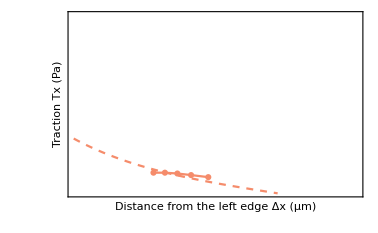

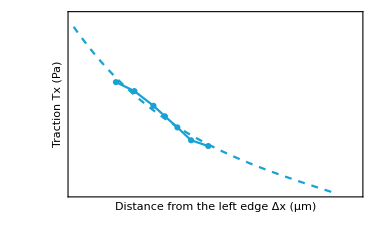

{{ζi0def→0.00286914,ζigrad→0.0000587495}}

{{ξ0def→2.2,ξgrad→0.001}}

```mathematica
(* EXPERIMENTAL DATA and some model parameters *)
R = 30; (* Radius of clusters from Fig. 1g,h *)
x0idef = 0;
x0 = 0; 
E0 = 0.5;
(* Egrad = 0.033;*)
ζigrad = 0; 
θ1 = 134; (* θ[(1-E0)/Egrad + x0idef]; *)
L01 = R*(Sin[(180-θ1) Degree]);
θ6 = θ[(6-E0)/Egrad + x0idef];
L06 = R*(Sin[(180-θ6) Degree]);
Print["L01 = ", N[L01], ", θ1 = ", θ1];
Print["L06 = ", N[L06], ", θ6 = ", θ6];

TracExp6 = {{4.47,43.70},{6.42,40.18},{8.44,34.40},{9.65,30.28},{10.97,25.91},{12.42,20.85},{14.24,18.58}};
TracExp6Fit =Transpose[{TracExp6[[All,1]]-L06,TracExp6[[All,2]]}]; (* From the left edge to the center (so that tractions are positive) *)
TracExp1 = {(*{6.42,8.24},*){8.44,8.11},{9.65,8.11},{10.97,7.79},{12.42,7.17},{14.24,6.36}};
TracExp1Fit =Transpose[{TracExp1[[All,1]]-L01,TracExp1[[All,2]]}];

h = 5;
η = 20000;
P1 = 0.01; (* Plinear[(1-E0)/Egrad+x0idef,x0idef,P0def,Pgrad]; *)
P6 = 0.05; (* Plinear[(6-E0)/Egrad+x0idef,x0idef,P0def,Pgrad]; *)  
ζ = -2;
Print["P1 = ", P1, ", P6 = ", P6];

ξ0def = 0.22;
ξgrad = 0.0001;
Print["ξ = ", ξ0def, ", ξgrad = ", ξgrad];
λ1 = Sqrt[2*2000/ξlinear[(1-E0)/Egrad+x0idef,x0idef,ξ0def,ξgrad]];
λ6 = Sqrt[2*2000/ξlinear[(6-E0)/Egrad+x0idef,x0idef,ξ0def,ξgrad]]; 
Print["λ1 = ", λ1, ", λ6 = ", λ6];

(* FindFit of the other parameters *)
Clear[Lc,ζi6,ζi1];
(* Clear[λ1,λ6]; *) 
fit6 = FindFit[TracExp6Fit, {1000*TEgrad[x,x0,x0idef,L06,Lc,ζi6,ζigrad,ζ,η,λ6,P6,R,h], 1<Lc<L06, 0.0001<ζi6<0.5 (*1<λ6<2000*)}, {Lc,ζi6}, x]
Lc = fit6[[1,2]];
ζi6 = fit6[[2,2]];
(* λ6 = fit6[[3,2]]; *)
fit1 = FindFit[TracExp1Fit, {1000*TEgrad[x,x0,x0idef,L01,Lc,ζi1,ζigrad,ζ,η,λ1,P1,R,h], 0.0001<ζi1<0.5 (*,1<λ1<2000*)}, {ζi1}, x]
ζi1 = fit1[[1,2]];
(* λ1 = fit1[[2,2]]; *) 

(* PLOT *)
s[j_] := Table[{j i, j i, {0, 0.01}}, {i, -100, 100}];
p[j_] := Table[{j i/2, "", {0, 0.01}}, {i, -99, 99}];
ticks[j_] := ArrayFlatten[{{s[j]}, {p[j]}}];

Show[{
ListPlot[{TracExp1Fit},
PlotRange->{{-L01,30-L01},{0,70}},Joined->True,PlotMarkers->Automatic,PlotStyle->RGBColor[0.96,0.55,0.42],
Frame->True,FrameStyle->Black,BaseStyle->{FontFamily -> "Calibri"},
Axes->False,
FrameTicks->{{ticks[10], None}, {ticks[4], None}}, FrameTicksStyle->Directive[16],
FrameLabel->{Style["Distance from the left edge Δx (µm)",14], Style["Traction Tx (Pa)",14]}],

Plot[1000*TEgrad[x,x0,x0idef,L01,Lc,ζi1,ζigrad,ζ,η,λ1,P1,R,h],{x,-L01,0},
PlotRange->{{-L01,30-L01},{0,70}},PlotStyle->{RGBColor[0.96,0.55,0.42],Dashed},
Frame->True,FrameStyle->Black,BaseStyle->{FontFamily -> "Calibri"},
FrameTicks->{{ticks[10], None}, {ticks[4], None}}, FrameTicksStyle->Directive[16],
FrameLabel->{Style["Distance from the left edge Δx (µm)",14], Style["Traction Tx (Pa)",14]}]
}]

Show[{
ListPlot[{TracExp6Fit},
PlotRange->{{-L06,30-L06},{0,70}},Joined->True,PlotMarkers->Automatic,PlotStyle->RGBColor[0.09,0.63,0.83],
Frame->True,FrameStyle->Black,BaseStyle->{FontFamily -> "Calibri"},
FrameTicks->{{ticks[10], None}, {ticks[4], None}}, FrameTicksStyle->Directive[16],
FrameLabel->{Style["Distance from the left edge Δx (µm)",14], Style["Traction Tx (Pa)",14]}],

Plot[1000*TEgrad[x,x0,x0idef,L06,Lc,ζi6,ζigrad,ζ,η,λ6,P6,R,h],{x,-L06,0},
PlotRange->{{-L06,30-L06},{0,70}},PlotStyle->{RGBColor[0.09,0.63,0.83],Dashed},
Frame->True,FrameStyle->Black,BaseStyle->{FontFamily -> "Calibri"},
FrameTicks->{{ticks[10], None}, {ticks[4], None}}, FrameTicksStyle->Directive[16],
FrameLabel->{Style["Distance from the left edge Δx (µm)",14], Style["Traction Tx (Pa)",14]}]
}]

Clear[ζi0def,ζigrad];
Solve[{ζi1 == ζi0def + ζigrad*((1-E0)/Egrad + x0idef), ζi6 == ζi0def + ζigrad*((6-E0)/Egrad + x0idef)}, {ζi0def,ζigrad}]
Clear[ξ0def,ξgrad];
Solve[{λ1 == Sqrt[2*η/(ξ0def + ξgrad*((1-E0)/Egrad + x0idef))], λ6 == Sqrt[2*η/(ξ0def + ξgrad*((6-E0)/Egrad + x0idef))]}, {ξ0def,ξgrad}] 

(* ERROR 
ζigrad = 0; 
Total[(1000*TEgrad[TracExp6Fit[[All,1]],x0,x0idef,L06,Lc,ζi6,ζigrad,ζ,η,λ6,P6,R,h]-TracExp6Fit[[All,2]])^2];
Total[(1000*TEgrad[TracExp1Fit[[All,1]],x0,x0idef,L01,Lc,ζi1,ζigrad,ζ,η,λ1,P1,R,h]-TracExp1Fit[[All,2]])^2]; *)
```

### Time evolution functions

#### Linear profiles (traction, friction, pressure and surface tension)

```mathematica
(***************** With LINEAR profiles of traction and friction ******************) 
(*   Initial L0 and H, impose volume conservation and evolve H and R accordingly  *) 
(*   Either analytical velocity (for ζigrad=ξgrad=0: indAnNum==1, for ζigrad!=0: 2) or numerical (else, indAnNum≠1,2)   *) 
evolutionVOLUMElinear[indAnNum_,t0_,tmax_,Δt_,x0i_,x0idef_,L0i_,Lci_,ζi0def_,ζigrad_,ζ_,η_,ξ0def_,ξgrad_,P0def_,Pgrad_,Hi_,h_]:=(
	L0critinc = Null; 
	L0critstarcalc = Null;
	prec = 0.1;
	Lc = Lci;
	x0 = x0i;
	(* If monostiffness substrate (indAnNum==1), set to 0 the initial position (choice of reference frame) *)
	indcheck=1;
	If[indAnNum==1, 
		{x0 = 0;
		If[ζigrad!=0 || ζigrad!=0,
		{Print["Error! Not monostiffness: ζigrad or ξgrad are different to 0"];
		indcheck=0}]}
	];
	If[indAnNum==2 && ξgrad!=0,
		{Print["Error! No anlaytical formula: ξgrad is different to 0"];
		indcheck=0}
	];
	(* Definition of the vector variables, positions and velocities. Time in hours for betters plots *)
	Clear[time,xrightev,xleftev,x0ev,L0ev,vrightev,vleftev,vx0ev,vL0ev,Hev,θev,Pev,Lc];
	time = {t0/3600}; 
	xrightev = {x0+L0i}; 
	xleftev = {x0-L0i};
	x0ev = {x0};
	L0ev = {L0i};
	vrightev = vleftev = vx0ev = vL0ev = {};
	Hev = {Hi};
	θev = Pev = {};
	(* Compute the radius and print the volume, and append the pressure. *) 
	V = VolumeCluster[L0i,Hi];
	Print["Cluster's volume = ", N[V], "µm^3"];
	R = (Hi^2+L0i^2)/(2*Hi);
	Rev = {R};
	P = Plinear[x0,x0idef,P0def,Pgrad];
	If[Hi>R, 
		{auxwet = 0;          (* auxwet == 1 for a wet state, 0 for a dewet state *) 
		AppendTo[θev, π-ArcSin[L0i/R]];
		AppendTo[Pev, P]},    (* if dewet state, P>0 + since γ is pointing outwards *) 
		{auxwet = 1; 
		AppendTo[θev, ArcSin[L0i/R]];
		AppendTo[Pev, -P]}    (* if wet state, P<0 + since γ is pointing inwards *) 
	];
	If[indcheck==1,
	(* Evoltuion: Euler's integration method *) 
	For[i=1, i≤tmax/Δt, i=i+1,  
		If[Esubstrate[x0ev[[-1]],x0idef,E0,Egrad]>Emax, Break[]];
		Lc = Lci;
		If[Lc>L0ev[[-1]], Lc=L0ev[[-1]]];
		AppendTo[time,t0+i*Δt/3600]; 
		(* Print every 50 hours *)
		If[Divisible[i*Δt,3600*50], Print["t = ", t0+i*Δt/3600, " h, E = ", Esubstrate[x0ev[[-1]],x0idef,E0,Egrad], " kPa and L0 = ", L0ev[[-1]], "µm"]]; 
		(* Calculate the velocities *) 	
		If[indAnNum==1,   
			(* Analytical and monostiffness solution (ξgrad=ζigrad=0): for equilibrium contact angle *) 
			{vright = Re[v1[xrightev[[-1]],L0ev[[-1]],Lc,ζi0def,ζ,Sqrt[2*η/ξ0def],η,Pev[[-1]],Rev[[-1]],h]];   (* Re only because when L0=R, numerical error that may take the sqrt of a negative very small number (10^(-15)) *)
			vleft = Re[v1[xleftev[[-1]],L0ev[[-1]],Lc,ζi0def,ζ,Sqrt[2*η/ξ0def],η,Pev[[-1]],Rev[[-1]],h]]},     (* 2γ/R = P *)
			{If[indAnNum==2, 
				(* Analytical solution with traction gradient, only if ξgrad=0 *)
				{vright = Re[vEgradfun[xrightev[[-1]],x0ev[[-1]],x0idef,L0ev[[-1]],Lc,ζi0def,ζigrad,ζ,η,Sqrt[2*η/ξ0def],Pev[[-1]],Rev[[-1]],h]];
				vleft = Re[vEgradfun[xleftev[[-1]],x0ev[[-1]],x0idef,L0ev[[-1]],Lc,ζi0def,ζigrad,ζ,η,Sqrt[2*η/ξ0def],Pev[[-1]],Rev[[-1]],h]];},
				(* Numerical solution otherwise *)
				{Clear[vND];
				vND = NDSolveValue[{2*η*v''[x]-v[x]*ξlinear[x,x0idef,ξ0def,ξgrad]==p[x,x0ev[[-1]],L0ev[[-1]],Lc]*(2*ζ*D[p[x,x0ev[[-1]],L0ev[[-1]],Lc],x]-ζilinear[x,x0idef,ζi0def,ζigrad]),
				(D[v[x],x]/.x->xleftev[[-1]])==(ζ+Pev[[-1]]*Rev[[-1]]/(2*Min[L0ev[[-1]],h])*Sqrt[1-(L0ev[[-1]]/Rev[[-1]])^2])/(2*η), 
				(D[v[x],x]/.x->xrightev[[-1]])==(ζ+Pev[[-1]]*Rev[[-1]]/(2*Min[L0ev[[-1]],h])*Sqrt[1-(L0ev[[-1]]/Rev[[-1]])^2])/(2*η)},
				v,{x,xleftev[[-1]],xrightev[[-1]]},AccuracyGoal->15,PrecisionGoal->10];
				vright = vND[xrightev[[-1]]];
				vleft = vND[xleftev[[-1]]]}];
			}
		];
		(* Append to velocity vectors and positions *) 
		AppendTo[vrightev, vright];
		AppendTo[xrightev, xrightev[[-1]] + vright*Δt];
		AppendTo[vleftev, vleft];
		AppendTo[xleftev, xleftev[[-1]] + vleft*Δt]; 
		AppendTo[L0ev, (xrightev[[-1]] - xleftev[[-1]])/2];
		AppendTo[x0ev, (xrightev[[-1]] + xleftev[[-1]])/2];
		AppendTo[vx0ev, (vrightev[[-1]] + vleftev[[-1]])/2];   
		AppendTo[vL0ev, (vrightev[[-1]] - vleftev[[-1]])/2];   
		(* Calculate the height and then the radius that keeps the volume constant after having evolved L0 *) 
		Clear[H];
		H = Solve[VolumeCluster[L0ev[[-1]],H]==V,H,Reals][[1]][[1,2]];
		AppendTo[Hev,H];
		AppendTo[Rev,(H^2+L0ev[[-1]]^2)/(2*H)];
		(* Save the new pressure, corresponding to the pressure in the CM of the cluster *)
		P = Plinear[x0ev[[-1]],x0idef,P0def,Pgrad]; 
		If[H>Rev[[-1]], 
			{AppendTo[θev, π-ArcSin[L0ev[[-1]]/Rev[[-1]]]];
			AppendTo[Pev, P];
			If[auxwet==1, (* when it changes from wet to dewet, print it and check the volume is the same *) 
				auxwet=0; 
				Print["At time ", N[time[[-1]]], "h, and position x0 = ", x0ev[[-1]], "µm, it goes from wet to DEWET and V .10= ", N[VolumeWet[Rev[[-1]],L0ev[[-1]]]], "µm^3"]
			]},
			{AppendTo[θev, ArcSin[L0ev[[-1]]/Rev[[-1]]]];
			AppendTo[Pev, -P];
			If[auxwet==0, (* same but from dewet to wet *) 
				auxwet=1; 
				Print["At time ", N[time[[-1]]], "h, and position x0 = ", x0ev[[-1]], "µm, it goes from dewet to WET and V .10= ", N[VolumeWet[Rev[[-1]],L0ev[[-1]]]], "µm^3"]
			]};
		];
		(* Find where L0 increases after decreasing if we have not already found it *) 
		If[L0critinc==Null && L0ev[[-1]]>L0ev[[-2]] && L0ev[[-1]]>prec,
			L0critinc = L0ev[[-2]]; 
			 If[i==1, Print["Starting with L0i = ", L0i, " the size always increases"], 
			 Print["Starting with L0i = ", L0i, " the size increases when it reaches L0 = ", L0critinc, " µm at time ", N[time[[-1]]], "h, position x0 = ", x0ev[[-1]]  ,"µm (traction ", ζilinear[x0ev[[-1]],x0idef,ζi0def,ζigrad], "kPa/µm and stiffness ", Esubstrate[x0ev[[-1]],x0idef,E0,Egrad], " kPa)"]];
		]; 
		(* Stop if H or L0 are smaller than precision *)   
		If[L0ev[[-1]]<prec, Print["Full dewetting (L0<", prec, "µm) at t = ", N[time[[-1]]], "h"]; Break[]];
		If[Hev[[-1]]<prec, Print["Full wetting (H<", prec, "µm) at t = ", N[time[[-1]]], "h"]; Break[]];
	];
	(* If for any time we have not found an increase in L0 *) 
	If[L0critinc==Null && Hev[[-1]]>prec && L0ev[[-1]]>prec, 
		L0critstarcalc = L0i;
		Print["Starting with L0i = ", L0i, " the size always decreases"];
	];
	];
);

(****** Linear profiles but with constant surface tension γP (used in monostiffness gels) ************) 
(*   Either analytical velocity (for ζigrad=ξgrad=0: indAnNum==1, for ζigrad!=0: 2) or numerical (else, indAnNum≠1,2)   *) 
evolutionVOLUMElinearConstγ[indAnNum_,t0_,tmax_,Δt_,x0i_,x0idef_,L0i_,Lci_,ζi0def_,ζigrad_,ζ_,η_,ξ0def_,ξgrad_,Hi_,γP_,h_]:=(
	L0critinc = Null; 
	L0critstarcalc = Null;
	prec = 0.1;
	Lc = Lci;
	x0 = x0i;
	indcheck=1;
	(* If monostiffness substrate (indAnNum==1), set to 0 the initial position (choice of reference frame) *)
	If[indAnNum==1, 
		{x0 = 0;
		If[ζigrad!=0 || ξgrad!=0,
		{Print["Error! Not monostiffness: ζigrad or ξgrad are different to 0"];
		indcheck=0}]}
	];
	If[indAnNum==2 && ξgrad!=0,
		{Print["Error! No analytical formula: ξgrad different to 0"];
		indcheck=0}
	];
	(* Definition of the vector variables, positions and velocities *)
	Clear[time,xrightev,xleftev,x0ev,L0ev,vrightev,vleftev,vx0ev,vL0ev,Hev,γPev,θev,Lc];
	time = {t0/3600}; 
	xrightev = {x0+L0i}; 
	xleftev = {x0-L0i};
	x0ev = {x0};
	L0ev = {L0i};
	vrightev = vleftev = vx0ev = vL0ev = {};
	Hev = {Hi};
	θev = γPev = {};
	(* Compute the radius and print the volume, and append the pressure. *) 
	V = VolumeCluster[L0i,Hi]; 
	Print["Cluster's volume = ", N[V], "µm^3"];
	R = (Hi^2+L0i^2)/(2*Hi);
	Rev = {R};
	If[Hi>R, 
		{auxwet = 0;       
		AppendTo[θev, π-ArcSin[L0i/R]];
		AppendTo[γPev, γP]}, 
		{auxwet = 1; 
		AppendTo[θev, ArcSin[L0i/R]];
		AppendTo[γPev, -γP]}
	];  
	If[indcheck==1,
	(* Evoltuion: Euler's integration method *) 
	For[i=1, i≤tmax/Δt, i=i+1,  
		(* Lc not to be larger than L0 *) 
		Lc = Lci;
		If[Lc>L0ev[[-1]], Lc=L0ev[[-1]]];
		AppendTo[time,t0+i*Δt/3600]; 
		(* Print every 50 hours *)
		If[Divisible[i*Δt,3600*50], Print["t = ", t0+i*Δt/3600, "h and L0 = ", L0ev[[-1]], "µm"]]; 
		(* Calculate the velocities *) 
		If[indAnNum==1,   
			(* Analytical and monostiffness solution (ξgrad=ζigrad=0): for equilibrium contact angle *) 
			{vright = Re[v1[xrightev[[-1]],L0ev[[-1]],Lc,ζi0def,ζ,Sqrt[2*η/ξ0def],η,2*γPev[[-1]]/Rev[[-1]],Rev[[-1]],h]];   (* Re only because when L0=R, numerical error that may take the sqrt of a negative very small number (10^(-15)) *)
			vleft = Re[v1[xleftev[[-1]],L0ev[[-1]],Lc,ζi0def,ζ,Sqrt[2*η/ξ0def],η,2*γPev[[-1]]/Rev[[-1]],Rev[[-1]],h]]},     (* 2γ/R = P *)
			{If[indAnNum==2, 
				(* Analytical solution with traction gradient, only if ξgrad=0 *)
				{vright = Re[vEgradfunγP[xrightev[[-1]],x0ev[[-1]],x0idef,L0ev[[-1]],Lc,ζi0def,ζigrad,ζ,η,Sqrt[2*η/ξ0def],γPev[[-1]],Rev[[-1]],h]];
				vleft = Re[vEgradfunγP[xleftev[[-1]],x0ev[[-1]],x0idef,L0ev[[-1]],Lc,ζi0def,ζigrad,ζ,η,Sqrt[2*η/ξ0def],γPev[[-1]],Rev[[-1]],h]];},
				(* Numerical solution otherwise *)
				{Clear[vND];
				vND = NDSolveValue[{2*η*v''[x]-v[x]*ξlinear[x,x0idef,ξ0def,ξgrad]==p[x,x0ev[[-1]],L0ev[[-1]],Lc]*(2*ζ*D[p[x,x0ev[[-1]],L0ev[[-1]],Lc],x]-ζilinear[x,x0idef,ζi0def,ζigrad]),
				(D[v[x],x]/.x->xleftev[[-1]])==(ζ+γPev[[-1]]/Min[L0ev[[-1]],h]*Sqrt[1-(L0ev[[-1]]/Rev[[-1]])^2])/(2*η), 
				(D[v[x],x]/.x->xrightev[[-1]])==(ζ+γPev[[-1]]/Min[L0ev[[-1]],h]*Sqrt[1-(L0ev[[-1]]/Rev[[-1]])^2])/(2*η)},
				v,{x,xleftev[[-1]],xrightev[[-1]]},AccuracyGoal->15,PrecisionGoal->10];
				vright = vND[xrightev[[-1]]];
				vleft = vND[xleftev[[-1]]]}];
			}
		];
		(* Append to velocity vectors and positions *) 
		AppendTo[vrightev, vright];
		AppendTo[xrightev, xrightev[[-1]] + vright*Δt];
		AppendTo[vleftev, vleft];
		AppendTo[xleftev, xleftev[[-1]] + vleft*Δt]; 
		AppendTo[L0ev, (xrightev[[-1]] - xleftev[[-1]])/2];
		AppendTo[x0ev, (xrightev[[-1]] + xleftev[[-1]])/2];
		AppendTo[vx0ev, (vrightev[[-1]] + vleftev[[-1]])/2];    
		AppendTo[vL0ev, (vrightev[[-1]] - vleftev[[-1]])/2];  
		(* Calculate the height and then the radius that keeps the volume constant after having evolved L0 *) 
		Clear[H];
		H = Solve[VolumeCluster[L0ev[[-1]],H]==V,H,Reals][[1]][[1,2]];
		AppendTo[Hev,H];
		AppendTo[Rev,(H^2+L0ev[[-1]]^2)/(2*H)];
		(* Save the new gamma, corresponding to the surface tension in the CM of the cluster *)
		If[H>Rev[[-1]], 
			{AppendTo[θev, Re[π-ArcSin[L0ev[[-1]]/Rev[[-1]]]]];
			AppendTo[γPev, γP]; 
			If[auxwet==1 && Abs[Hev[[-1]]-Rev[[-1]]]>10^(-7),  (* only if we are not exactly at 90.ba, which happens if H==R but for avoiding numerica errors we put a precision *) 
				auxwet=0; 
				Print["At time ", N[time[[-1]]], "h, and position x0 = ", x0ev[[-1]], "µm (i = ", i, "), it goes from wet to DEWET and V .10= ", N[VolumeWet[Rev[[-1]],L0ev[[-1]]]], "µm^3"]
			]},
			{AppendTo[θev, Re[ArcSin[L0ev[[-1]]/Rev[[-1]]]]];
			AppendTo[γPev, -γP];
			If[auxwet==0 && Abs[Hev[[-1]]-Rev[[-1]]]>10^(-7), 
				auxwet=1; 
				Print["At time ", N[time[[-1]]], "h, and position x0 = ", x0ev[[-1]], "µm (i = ", i, "), it goes from dewet to WET and V .10= ", N[VolumeWet[Rev[[-1]],L0ev[[-1]]]], "µm^3"]
			]};
		];
		(* Find where L0 increases after decreasing if we have not already found it *) 
		If[L0critinc==Null && L0ev[[-1]]>L0ev[[-2]] && L0ev[[-1]]>prec,
			L0critinc = L0ev[[-2]]; 
			If[i==1, Print["Starting with L0i = ", L0i, " the size always increases"], 
			Print["Starting with L0i = ", L0i, " the size increases when it reaches L0 = ", L0critinc, " µm at time ", N[time[[-1]]], " hours, position x0 = ", x0ev[[-1]]  ,"µm (traction ", ζilinear[x0ev[[-1]],x0idef,ζi0def,ζigrad], "kPa/µm and stiffness ", Esubstrate[x0ev[[-1]],x0idef,E0,Egrad], "kPa)"]];
		]; 
		(* Stop if H or L0 are smaller than precision *)   
		If[L0ev[[-1]]<prec, Print["Full dewetting (L0<", prec, "µm) at t = ", N[time[[-1]]], "h"]; Break[]];
		If[Hev[[-1]]<prec, Print["Full wetting (H<", prec, "µm) at t = ", N[time[[-1]]], "h"]; Break[]];
	];
	(* If for any time we have not found an increase in L0 *) 
	If[L0critinc==Null && Hev[[-1]]>prec && L0ev[[-1]]>prec, 
		L0critstarcalc = L0i;
		Print["Starting with L0i = ", L0i, " the size always decreases"]; 
	];
	];
);
```

#### Saturated profiles (traction and friction) and either linear or saturated pressure (or surface tension)

```mathematica
(* SATURATED friction and traction, linear pressure *)  
evolutionVOLUMEsaturated[t0_,tmax_,Δt_,Emax_,x0i_,x0idef_,L0i_,Lci_,E0_,Egrad_,Estar_,a_,ζ_,η_,ξ0def_,Estar2_,a2_,P0def_,Pgrad_,Hi_,h_,αζi_,αP_]:=(
	L0critinc = Null; 
	L0critstarcalc = Null;
	prec = 0.1;
	Lc = Lci;
	(* Definition of the vector variables, positions and velocities *)
	Clear[time,xrightev,xleftev,x0ev,L0ev,vrightev,vleftev,vx0ev,vL0ev,Hev,θev,Pev,Lc];
	time = {t0/3600}; 
	xrightev = {x0i+L0i}; 
	xleftev = {x0i-L0i};
	x0ev = {x0i};
	L0ev = {L0i};
	vrightev = vleftev = vx0ev = vL0ev = {};
	Hev = {Hi};
	θev = Pev = {};
	V = VolumeCluster[L0i,Hi]; 
	Print["Cluster's volume = ", N[V], "µm^3"];
	R = (Hi^2+L0i^2)/(2*Hi);
	Rev = {R};
	P = αP*Plinear[x0i,x0idef,P0def,Pgrad];   	
	If[Hi>R, 
		{auxwet = 0;     
		AppendTo[θev, π-ArcSin[L0i/R]];
		AppendTo[Pev, P]}, 
		{auxwet = 1; 
		AppendTo[θev, ArcSin[L0i/R]];
		AppendTo[Pev, -P]}
	];  
	(* Evoltuion: Euler's integration method *) 
	For[i=1, i≤tmax/Δt, i=i+1,  
		If[Esubstrate[x0ev[[-1]],x0idef,E0,Egrad]>Emax, Break[]];
		Lc = Lci;
		If[Lc>L0ev[[-1]], Lc=L0ev[[-1]]];
		AppendTo[time,t0+i*Δt/3600]; 
		(* Print every 50 hours *)
		If[Divisible[i*Δt,3600*50], Print["t = ", t0+i*Δt/3600, " h, E = ", Esubstrate[x0ev[[-1]],x0idef,E0,Egrad], " kPa and L0 = ", L0ev[[-1]], "µm"]]; 
		(* Calculate the velocities *) 
		Clear[vND];
		vND = NDSolveValue[{2*η*v''[x]-v[x]*ξsat[Esubstrate[x,x0idef,E0,Egrad],a2,Estar2,ξ0def]==p[x,x0ev[[-1]],L0ev[[-1]],Lc]*(2*ζ*D[p[x,x0ev[[-1]],L0ev[[-1]],Lc],x]-αζi*ζisat[Esubstrate[x,x0idef,E0,Egrad],a,Estar]),
		(D[v[x],x]/.x->xleftev[[-1]])==(ζ+Pev[[-1]]*Rev[[-1]]/(2*Min[L0ev[[-1]],h])*Sqrt[1-(L0ev[[-1]]/Rev[[-1]])^2])/(2*η), 
		(D[v[x],x]/.x->xrightev[[-1]])==(ζ+Pev[[-1]]*Rev[[-1]]/(2*Min[L0ev[[-1]],h])*Sqrt[1-(L0ev[[-1]]/Rev[[-1]])^2])/(2*η)},
		v,{x,xleftev[[-1]],xrightev[[-1]]},AccuracyGoal->15,PrecisionGoal->10];
		vright = vND[xrightev[[-1]]];   (* if we use NDSolve instaed of NDSolveValue, put vright = (Evaluate[v[x]/. vND]/.x->(x0+L0))[[1]]*3600 *)
		vleft = vND[xleftev[[-1]]];
		(* Append to velocity vectors and positions *) 
		AppendTo[vrightev, vright];
		AppendTo[xrightev, xrightev[[-1]] + vright*Δt];
		AppendTo[vleftev, vleft];
		AppendTo[xleftev, xleftev[[-1]] + vleft*Δt]; 
		AppendTo[L0ev, (xrightev[[-1]] - xleftev[[-1]])/2];
		AppendTo[x0ev, (xrightev[[-1]] + xleftev[[-1]])/2];
		AppendTo[vx0ev, (vrightev[[-1]] + vleftev[[-1]])/2];   
		AppendTo[vL0ev, (vrightev[[-1]] - vleftev[[-1]])/2];   
		(* Calculate the height and then the radius that keeps the volume constant after having evolved L0 *) 
		Clear[H];
		H = Solve[VolumeCluster[L0ev[[-1]],H]==V,H,Reals][[1]][[1,2]];
		AppendTo[Hev,H];
		AppendTo[Rev,(H^2+L0ev[[-1]]^2)/(2*H)];
		(* Save the new pressure, corresponding to the pressure in the CM of the cluster *)
		P = αP*Plinear[x0ev[[-1]],x0idef,P0def,Pgrad];  
		If[H>Rev[[-1]], 
			{AppendTo[θev, π-ArcSin[L0ev[[-1]]/Rev[[-1]]]];
			AppendTo[Pev, P];
			If[auxwet==1, 
				auxwet=0; 
				Print["At time ", N[time[[-1]]], " hours, and position x0 = ", x0ev[[-1]], "µm, it goes from wet to DEWET and V .10= ", N[VolumeWet[Rev[[-1]],L0ev[[-1]]]], "µm^3"]
			]},
			{AppendTo[θev, ArcSin[L0ev[[-1]]/Rev[[-1]]]];
			AppendTo[Pev, -P];
			If[auxwet==0,  
				auxwet=1; 
				Print["At time ", N[time[[-1]]], " hours, and position x0 = ", x0ev[[-1]], "µm, it goes from dewet to WET and V .10= ", N[VolumeWet[Rev[[-1]],L0ev[[-1]]]], "µm^3"]
			]};
		];
		(* Find where L0 increases after decreasing if we have not already found it *) 
		If[L0critinc==Null && L0ev[[-1]]>L0ev[[-2]] && L0ev[[-1]]>prec,
			L0critinc = L0ev[[-2]]; 
			 If[i==1, Print["Starting with L0i = ", L0i, " the size always increases"], 
			 Print["Starting with L0i = ", L0i, " the size increases when it reaches L0 = ", L0critinc, "µm at time ", N[time[[-1]]], "h, position x0 = ", x0ev[[-1]], "µm (traction ", αζi*ζisat[Esubstrate[x0ev[[-1]],x0idef,E0,Egrad],a,Estar], "kPa/µm and stiffness ", Esubstrate[x0ev[[-1]],x0idef,E0,Egrad], " kPa)"]];	
		]; 
		(* Stop if H or L0 are smaller than precision *)   
		If[L0ev[[-1]]<prec, Print["Full dewetting (L0<", prec, "µm) at t = ", N[time[[-1]]], "h"]; Break[]];
		If[Hev[[-1]]<prec, Print["Full wetting (H<", prec, "µm) at t = ", N[time[[-1]]], "h"]; Break[]];
	];
	(* If for any time we have not found an increase in L0 *) 
	If[L0critinc==Null && Hev[[-1]]>prec && L0ev[[-1]]>prec, 
		L0critstarcalc = L0i;
		Print["Starting with L0i = ", L0i, " the size always decreases"]; 
	];
);


(* Saturated profiles of traction and friction but linear surface tension *) 
evolutionVOLUMEsaturatedγ[t0_,tmax_,Δt_,Emax_,x0i_,x0idef_,L0i_,Lci_,E0_,Egrad_,Estar_,a_,ζ_,η_,ξ0def_,Estar2_,a2_,γ0def_,γgrad_,Hi_,h_,αζi_,αP_]:=(
	L0critinc = Null; 
	L0critstarcalc = Null;
	prec = 0.1;
	Lc = Lci;
	(* Definition of the vector variables, positions and velocities *)
	Clear[time,xrightev,xleftev,x0ev,L0ev,vrightev,vleftev,vx0ev,vL0ev,Hev,θev,γev,Lc];
	time = {t0/3600}; 
	xrightev = {x0i+L0i}; 
	xleftev = {x0i-L0i};
	x0ev = {x0i};
	L0ev = {L0i};
	vrightev = vleftev = vx0ev = vL0ev = {};
	Hev = {Hi};
	θev = γev = {};
	V = VolumeCluster[L0i,Hi]; 
	Print["Cluster's volume = ", N[V], "µm^3"];
	R = (Hi^2+L0i^2)/(2*Hi);
	Rev = {R};
	γ = αP*(γ0def + γgrad*(x0i-x0idef));
	If[Hi>R, 
		{auxwet = 0;     
		AppendTo[θev, π-ArcSin[L0i/R]];
		AppendTo[γev, γ]}, 
		{auxwet = 1; 
		AppendTo[θev, ArcSin[L0i/R]];
		AppendTo[γev, -γ]}
	];  
	(* Evoltuion: Euler's integration method *) 
	For[i=1, i≤tmax/Δt, i=i+1,  
		If[Esubstrate[x0ev[[-1]],x0idef,E0,Egrad]>Emax, Break[]];
		Lc = Lci;
		If[Lc>L0ev[[-1]], Lc=L0ev[[-1]]];
		AppendTo[time,t0+i*Δt/3600]; 
		(* Print every 50 hours *)
		If[Divisible[i*Δt,3600*50], Print["t = ", t0+i*Δt/3600, " h, E = ", Esubstrate[x0ev[[-1]],x0idef,E0,Egrad], " kPa and L0 = ", L0ev[[-1]], "µm"]]; 
		(* Calculate the velocities *) 
		Clear[vND];
		vND = NDSolveValue[{2*η*v''[x]-v[x]*ξsat[Esubstrate[x,x0idef,E0,Egrad],a2,Estar2,ξ0def]==p[x,x0ev[[-1]],L0ev[[-1]],Lc]*(2*ζ*D[p[x,x0ev[[-1]],L0ev[[-1]],Lc],x]-αζi*ζisat[Esubstrate[x,x0idef,E0,Egrad],a,Estar]),
		(D[v[x],x]/.x->xleftev[[-1]])==(ζ+γev[[-1]]/Min[L0ev[[-1]],h]*Sqrt[1-(L0ev[[-1]]/Rev[[-1]])^2])/(2*η),
		(D[v[x],x]/.x->xrightev[[-1]])==(ζ+γev[[-1]]/Min[L0ev[[-1]],h]*Sqrt[1-(L0ev[[-1]]/Rev[[-1]])^2])/(2*η)},
		v,{x,xleftev[[-1]],xrightev[[-1]]},AccuracyGoal->15,PrecisionGoal->10];
		vright = vND[xrightev[[-1]]];
		vleft = vND[xleftev[[-1]]];
		(* Append to velocity vectors and positions *) 
		AppendTo[vrightev, vright];
		AppendTo[xrightev, xrightev[[-1]] + vright*Δt];
		AppendTo[vleftev, vleft];
		AppendTo[xleftev, xleftev[[-1]] + vleft*Δt]; 
		AppendTo[L0ev, (xrightev[[-1]] - xleftev[[-1]])/2];
		AppendTo[x0ev, (xrightev[[-1]] + xleftev[[-1]])/2];
		AppendTo[vx0ev, (vrightev[[-1]] + vleftev[[-1]])/2];   
		AppendTo[vL0ev, (vrightev[[-1]] - vleftev[[-1]])/2];   
		(* Calculate the height and then the radius that keeps the volume constant after having evolved L0 *) 
		Clear[H];
		H = Solve[VolumeCluster[L0ev[[-1]],H]==V,H,Reals][[1]][[1,2]];
		AppendTo[Hev,H];
		AppendTo[Rev,(H^2+L0ev[[-1]]^2)/(2*H)];
		(* Save the new gamma, corresponding to the pressure in the CM of the cluster *)
		γ = αP*(γ0def + γgrad*(x0ev[[-1]]-x0idef));
		If[H>Rev[[-1]], 
			{AppendTo[θev, π-ArcSin[L0ev[[-1]]/Rev[[-1]]]];
			AppendTo[γev, γ];
			If[auxwet==1, 
				auxwet=0; 
				Print["At time ", N[time[[-1]]], " hours, and position x0 = ", x0ev[[-1]], "µm, it goes from wet to DEWET and V .10= ", N[VolumeWet[Rev[[-1]],L0ev[[-1]]]], "µm^3"]
			]},
			{AppendTo[θev, ArcSin[L0ev[[-1]]/Rev[[-1]]]];
			AppendTo[γev, -γ];
			If[auxwet==0,  
				auxwet=1; 
				Print["At time ", N[time[[-1]]], " hours, and position x0 = ", x0ev[[-1]], "µm, it goes from dewet to WET and V .10= ", N[VolumeWet[Rev[[-1]],L0ev[[-1]]]], "µm^3"]
			]};
		];
		(* Find where L0 increases after decreasing if we have not already found it *) 
		If[L0critinc==Null && L0ev[[-1]]>L0ev[[-2]] && L0ev[[-1]]>prec,
			L0critinc = L0ev[[-2]]; 
			 If[i==1, Print["Starting with L0i = ", L0i, " the size always increases"], 
			 Print["Starting with L0i = ", L0i, " the size increases when it reaches L0 = ", L0critinc, "µm at time ", N[time[[-1]]], "h, position x0 = ", x0ev[[-1]], "µm (traction ", αζi*ζisat[Esubstrate[x0ev[[-1]],x0idef,E0,Egrad],a,Estar], "kPa/µm and stiffness ", Esubstrate[x0ev[[-1]],x0idef,E0,Egrad], " kPa)"]];	
		]; 
		(* Stop if H or L0 are smaller than precision *)   
		If[L0ev[[-1]]<prec, Print["Full dewetting (L0<", prec, "µm) at t = ", N[time[[-1]]], "h"]; Break[]];
		If[Hev[[-1]]<prec, Print["Full wetting (H<", prec, "µm) at t = ", N[time[[-1]]], "h"]; Break[]];
	];
	(* If for any time we have not found an increase in L0 *) 
	If[L0critinc==Null && Hev[[-1]]>prec && L0ev[[-1]]>prec, 
		L0critstarcalc = L0i;
		Print["Starting with L0i = ", L0i, " the size always decreases"]; 
	];
);

(* Saturated friction, traction and pressure *)  
evolutionVOLUMEsaturatedAll[t0_,tmax_,Δt_,Emax_,x0i_,x0idef_,L0i_,Lci_,E0_,Egrad_,Estar_,a_,ζ_,η_,ξ0def_,Estar2_,a2_,aP_,EstarP_,Hi_,h_,αζi_,αP_]:=(
	L0critinc = Null; 
	L0critstarcalc = Null;
	prec = 0.1;
	Lc = Lci;
	(* Definition of the vector variables, positions and velocities *)
	Clear[time,xrightev,xleftev,x0ev,L0ev,vrightev,vleftev,vx0ev,vL0ev,Hev,θev,Pev,Lc];
	time = {t0/3600}; 
	xrightev = {x0i+L0i}; 
	xleftev = {x0i-L0i};
	x0ev = {x0i};
	L0ev = {L0i};
	vrightev = vleftev = vx0ev = vL0ev = {};
	Hev = {Hi};
	θev = Pev = {};
	V = VolumeCluster[L0i,Hi]; 
	Print["Cluster's volume = ", N[V], "µm^3"];
	R = (Hi^2+L0i^2)/(2*Hi);
	Rev = {R};
	P = αP*Psat[Esubstrate[x0i,x0idef,E0,Egrad],aP,EstarP];
	If[Hi>R, 
		{auxwet = 0;     
		AppendTo[θev, π-ArcSin[L0i/R]];
		AppendTo[Pev, P]}, 
		{auxwet = 1; 
		AppendTo[θev, ArcSin[L0i/R]];
		AppendTo[Pev, -P]}
	];  
	(* Evoltuion: Euler's integration method *) 
	For[i=1, i≤tmax/Δt, i=i+1,  
		If[Esubstrate[x0ev[[-1]],x0idef,E0,Egrad]>Emax, Break[]];
		Lc = Lci;
		If[Lc>L0ev[[-1]], Lc=L0ev[[-1]]];
		AppendTo[time,t0+i*Δt/3600]; 
		(* Print every 50 hours *)
		If[Divisible[i*Δt,3600*50], Print["t = ", t0+i*Δt/3600, " h, E = ", Esubstrate[x0ev[[-1]],x0idef,E0,Egrad], " kPa and L0 = ", L0ev[[-1]], "µm"]]; 
		(* Calculate the velocities *) 
		Clear[vND];
		vND = NDSolveValue[{2*η*v''[x]-v[x]*ξsat[Esubstrate[x,x0idef,E0,Egrad],a2,Estar2,ξ0def]==p[x,x0ev[[-1]],L0ev[[-1]],Lc]*(2*ζ*D[p[x,x0ev[[-1]],L0ev[[-1]],Lc],x]-αζi*ζisat[Esubstrate[x,x0idef,E0,Egrad],a,Estar]),
		(D[v[x],x]/.x->xleftev[[-1]])==(ζ+Pev[[-1]]*Rev[[-1]]/(2*Min[L0ev[[-1]],h])*Sqrt[1-(L0ev[[-1]]/Rev[[-1]])^2])/(2*η), (*Piecewise[{{L0ev[[-1]],L0ev[[-1]]<h},{h,L0ev[[-1]]>h}}]*)
		(D[v[x],x]/.x->xrightev[[-1]])==(ζ+Pev[[-1]]*Rev[[-1]]/(2*Min[L0ev[[-1]],h])*Sqrt[1-(L0ev[[-1]]/Rev[[-1]])^2])/(2*η)},
		v,{x,xleftev[[-1]],xrightev[[-1]]},AccuracyGoal->15,PrecisionGoal->10];
		vright = vND[xrightev[[-1]]];   (* if we use NDSolve instaed of NDSolveValue, put vright = (Evaluate[v[x]/. vND]/.x->(x0+L0))[[1]]*3600 *)
		vleft = vND[xleftev[[-1]]];
		(* Append to velocity vectors and positions *) 
		AppendTo[vrightev, vright];
		AppendTo[xrightev, xrightev[[-1]] + vright*Δt];
		AppendTo[vleftev, vleft];
		AppendTo[xleftev, xleftev[[-1]] + vleft*Δt]; 
		AppendTo[L0ev, (xrightev[[-1]] - xleftev[[-1]])/2];
		AppendTo[x0ev, (xrightev[[-1]] + xleftev[[-1]])/2];
		AppendTo[vx0ev, (vrightev[[-1]] + vleftev[[-1]])/2];   
		AppendTo[vL0ev, (vrightev[[-1]] - vleftev[[-1]])/2];   
		(* Calculate the height and then the radius that keeps the volume constant after having evolved L0 *) 
		Clear[H];
		H = Solve[VolumeCluster[L0ev[[-1]],H]==V,H,Reals][[1]][[1,2]];
		AppendTo[Hev,H];
		AppendTo[Rev,(H^2+L0ev[[-1]]^2)/(2*H)];
		(* Save the new pressure, corresponding to the pressure in the CM of the cluster *)
		P = αP*Psat[Esubstrate[x0ev[[-1]],x0idef,E0,Egrad],aP,EstarP]; 
		If[H>Rev[[-1]], 
			{AppendTo[θev, π-ArcSin[L0ev[[-1]]/Rev[[-1]]]];
			AppendTo[Pev, P];
			If[auxwet==1, 
				auxwet=0; 
				Print["At time ", N[time[[-1]]], " hours, and position x0 = ", x0ev[[-1]], "µm, it goes from wet to DEWET and V .10= ", N[VolumeWet[Rev[[-1]],L0ev[[-1]]]], "µm^3"]
			]},
			{AppendTo[θev, ArcSin[L0ev[[-1]]/Rev[[-1]]]];
			AppendTo[Pev, -P];
			If[auxwet==0,  
				auxwet=1; 
				Print["At time ", N[time[[-1]]], " hours, and position x0 = ", x0ev[[-1]], "µm, it goes from dewet to WET and V .10= ", N[VolumeWet[Rev[[-1]],L0ev[[-1]]]], "µm^3"]
			]};
		];
		(* Find where L0 increases after decreasing if we have not already found it *) 
		If[L0critinc==Null && L0ev[[-1]]>L0ev[[-2]] && L0ev[[-1]]>prec,
			L0critinc = L0ev[[-2]]; 
			 If[i==1, Print["Starting with L0i = ", L0i, " the size always increases"], 
			 Print["Starting with L0i = ", L0i, " the size increases when it reaches L0 = ", L0critinc, "µm at time ", N[time[[-1]]], "h, position x0 = ", x0ev[[-1]], "µm (traction ", αζi*ζisat[Esubstrate[x0ev[[-1]],x0idef,E0,Egrad],a,Estar], "kPa/µm and stiffness ", Esubstrate[x0ev[[-1]],x0idef,E0,Egrad], " kPa)"]];	
		]; 
		(* Stop if H or L0 are smaller than precision *)   
		If[L0ev[[-1]]<prec, Print["Full dewetting (L0<", prec, "µm) at t = ", N[time[[-1]]], "h"]; Break[]];
		If[Hev[[-1]]<prec, Print["Full wetting (H<", prec, "µm) at t = ", N[time[[-1]]], "h"]; Break[]];
	];
	(* If for any time we have not found an increase in L0 *) 
	If[L0critinc==Null && Hev[[-1]]>prec && L0ev[[-1]]>prec, 
		L0critstarcalc = L0i;
		Print["Starting with L0i = ", L0i, " the size always decreases"]; 
	];
);
```

## Results

### Equilibrium contact angle in a monostiffness substrate

#### Statics (θeq such that vspreading = 0)

Here, assuming substrates of uniform stiffness, we plot the spreading velocity for constant volume clusters.

```mathematica
(* Parameters *)
Lc = 15;
ζi0 = 0.03;
ζ = -2;
η = 20000;
ξ0 = 0.22;
γ = 0;
h = 5;

(* Find the critical size for the 2D active wetting transition --> no γ nor compressibility term and R=L0 (θ=90.ba) *)
L0crit = FindRoot[v1[L0,L0,Lc,ζi0,ζ,Sqrt[2*η/ξ0],η,0,L0,h] == 0,{L0,30,10,100},MaxIterations->100][[1,2]];
Print["2D γ=0: full dewetting below L0crit = ", L0crit, "µm, and full wetting above."]; 

(* Choose the volume at this critical size (θ = 90.ba to have γcosθ=0) *)
L0ref = L0crit;
Vconst = 2/3*π*L0ref^3;  (* (92500 π)/3 *)
Print["Volume = ", Vconst];
L0max = 150;
γ = 0;
```

2D γ=0: full dewetting below L0crit = 47.6489µm, and full wetting above.

Volume = 226578.

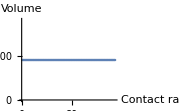

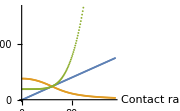

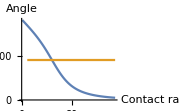

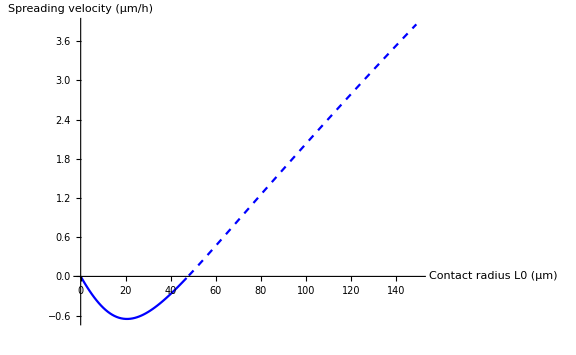

```mathematica
(* Plot spreading velocity for constant volume *)
L0list = Range[0.001,L0max,1];
L0listdw = L0listw = {};
Rlist = Rlistdw = Rlistw = Hlist = θlist = γauxdw = γauxw = {};
vlistdw = vlistw = {};
For[i=1, i<=Length[L0list], i=i+1,
	Clear[H];
	AppendTo[Hlist, NSolve[VolumeCluster[L0list[[i]], H]==Vconst, H, Reals][[1,1]][[2]]];
	AppendTo[Rlist, (Hlist[[i]]^2 + L0list[[i]]^2)/(2*Hlist[[i]])];
	If[Hlist[[i]]>L0list[[i]],
		{AppendTo[γauxdw, 1];  
		AppendTo[Rlistdw, Rlist[[i]]];
		AppendTo[L0listdw, L0list[[i]]]; 
		AppendTo[θlist, π-ArcSin[L0list[[i]]/Rlist[[i]]]];
		AppendTo[vlistdw, v1[L0list[[i]],L0list[[i]],Lc,ζi0,ζ,Sqrt[2*η/ξ0],η,2*γ/Rlist[[i]],Rlist[[i]],h]]}, 
		{AppendTo[γauxw, -1];
		AppendTo[Rlistw, Rlist[[i]]];
		AppendTo[L0listw, L0list[[i]]];
		AppendTo[θlist, ArcSin[L0list[[i]]/Rlist[[i]]]];
		AppendTo[vlistw, v1[L0list[[i]],L0list[[i]],Lc,ζi0,ζ,Sqrt[2*η/ξ0],η,-2*γ/Rlist[[i]],Rlist[[i]],h]]} 
	];
];  
ListPlot[VolumeCluster[L0list,Hlist],ImageSize->Small,AxesLabel->{"Contact radius","Volume"}]
ListPlot[{L0list,Hlist,Rlist},AxesLabel->{"Contact radius",None},PlotLegends->{"L0","H","R"},ImageSize->Small,PlotRange->Automatic]
ListPlot[{θlist*180/π,{{9,90},{L0max,90}}},Joined->True,AxesLabel->{"Contact radius","Angle"},PlotRange->All,ImageSize->Small]

ListPlot[{Transpose[{L0listdw,3600*vlistdw}],Transpose[{L0listw,3600*vlistw}]},
PlotRange->{{0,L0max},All}, 
Joined->True,
PlotStyle->{Blue,{Blue,Dashed}},
AxesLabel->{Style["Contact radius L0 (µm)",16,Black],Style["Spreading velocity (µm/h)",16,Black]},   
TicksStyle->Directive[17],
BaseStyle->{FontFamily->"Calibri"},
ImageSize->Large]
```

```mathematica
(* Find Roots *) 
RootL0 = FindRoot[Interpolation[Transpose[{Join[L0listdw,L0listw],Join[vlistdw,vlistw]}]][x],{x,1,140}][[1,2]]; (* change from here the boundaries *)
Clear[H];
RootH = NSolve[VolumeCluster[RootL0, H]==Vconst, H, Reals][[1,1]][[2]];
RootR = (RootH^2 + RootL0^2)/(2*RootH);
If[RootH > RootR, 
	Rootθ = π-ArcSin[RootL0/RootR],
	Rootθ = ArcSin[RootL0/RootR];
];  
Print["L0 = ", RootL0, " H = ", RootH, " R = ", RootR, " θ = ", Rootθ*180/π, " V = ", VolumeCluster[RootL0,RootH]]
```

L0 = 47.6489 H = 47.6489 R = 47.6489 θ = 90. V = 226578.

```mathematica
Manipulate[
argsdw = Transpose[{L0listdw,L0listdw,ConstantArray[Lc,Length[L0listdw]],ConstantArray[ζi0,Length[L0listdw]],ConstantArray[ζ,Length[L0listdw]],ConstantArray[Sqrt[2*η/ξ0],Length[L0listdw]],ConstantArray[η,Length[L0listdw]],2*γauxdw*γ/Rlistdw,Rlistdw,ConstantArray[h,Length[L0listdw]]}];
argsw = Transpose[{L0listw,L0listw,ConstantArray[Lc,Length[L0listw]],ConstantArray[ζi0,Length[L0listw]],ConstantArray[ζ,Length[L0listw]],ConstantArray[Sqrt[2*η/ξ0],Length[L0listw]],ConstantArray[η,Length[L0listw]],2*γauxw*γ/Rlistw,Rlistw,ConstantArray[h,Length[L0listw]]}];

ListPlot[{Transpose[{L0listdw,3600*v1@@@argsdw}],Transpose[{L0listw,3600*v1@@@argsw}]},
Joined->True,
PlotStyle->{Red,{Red,Dashed}},
PlotRange->{All,{-4,4}},
ImageSize->Large,
AxesLabel->{Style["Contact radius (µm)",16,Black],Style["Spreading velocity (µm/h)",16,Black]},   
TicksStyle->Directive[17],
BaseStyle->{FontFamily->"Calibri"}], 
{ξ0, 0.22,1},{ζi0,0.01,0.1},{γ,0,15}]
```

```mathematica
Manipulate[
argsdw = Table[Transpose[{L0listdw,L0listdw,ConstantArray[Lc,Length[L0listdw]],ConstantArray[ζi0,Length[L0listdw]],ConstantArray[ζ,Length[L0listdw]],ConstantArray[Sqrt[2*η/ξ0],Length[L0listdw]],ConstantArray[η,Length[L0listdw]],2*γauxdw*γ/Rlistdw,Rlistdw,ConstantArray[h,Length[L0listdw]]}], 
{γ,{0,1.5,2.5,3,4}}];
argsw = Table[Transpose[{L0listw,L0listw,ConstantArray[Lc,Length[L0listw]],ConstantArray[ζi0,Length[L0listw]],ConstantArray[ζ,Length[L0listw]],ConstantArray[Sqrt[2*η/ξ0],Length[L0listw]],ConstantArray[η,Length[L0listw]],2*γauxw*γ/Rlistw,Rlistw,ConstantArray[h,Length[L0listw]]}], 
{γ,{0,1.5,2.5,3,4}}];

ListPlot[{Transpose[{L0listdw,3600*v1@@@argsdw[[1]]}],Transpose[{L0listw,3600*v1@@@argsw[[1]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[2]]}],Transpose[{L0listw,3600*v1@@@argsw[[2]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[3]]}],Transpose[{L0listw,3600*v1@@@argsw[[3]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[4]]}],Transpose[{L0listw,3600*v1@@@argsw[[4]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[5]]}],Transpose[{L0listw,3600*v1@@@argsw[[5]]}],
{{30,-4},{30,4}}},
Joined->True,
PlotStyle->{ColorData[10,1],{ColorData[10,1],Dashed},
ColorData[10,2],{ColorData[10,2],Dashed},ColorData[10,3],{ColorData[10,3],Dashed},
ColorData[10,4],{ColorData[10,4],Dashed},ColorData[10,5],{ColorData[10,5],Dashed},
{Gray,Dashed}},
PlotLegends->{"γ = 0",None,"1.5",None,"2.5",None,"3",None,"4",None},
PlotRange->{{0,L0max},{-5,5}},
ImageSize->Large,
AxesLabel->{Style["Contact radius (µm)",16,Black],Style["Spreading velocity (µm/h)",16,Black]},   
TicksStyle->Directive[17],
BaseStyle->{FontFamily->"Calibri"}], 
{ζi0,0.001,1},{ξ0, 0.22}]
```

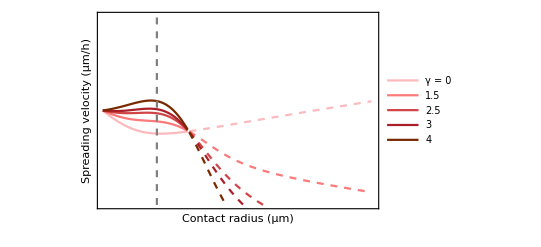

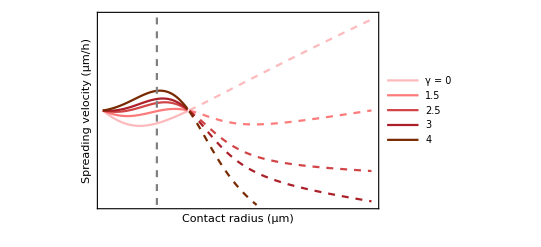

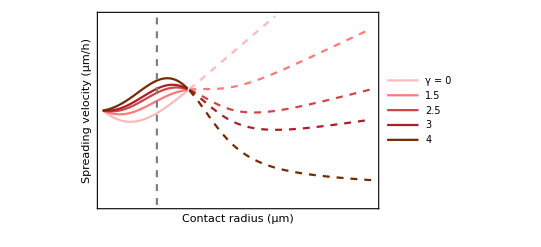

```mathematica
ζi0 = 0.01;
argsdw = Table[Transpose[{L0listdw,L0listdw,ConstantArray[Lc,Length[L0listdw]],ConstantArray[ζi0,Length[L0listdw]],ConstantArray[ζ,Length[L0listdw]],ConstantArray[Sqrt[2*η/ξ0],Length[L0listdw]],ConstantArray[η,Length[L0listdw]],2*γauxdw*γ/Rlistdw,Rlistdw,ConstantArray[h,Length[L0listdw]]}], 
{γ,{0,1.5,2.5,3,4}}];
argsw = Table[Transpose[{L0listw,L0listw,ConstantArray[Lc,Length[L0listw]],ConstantArray[ζi0,Length[L0listw]],ConstantArray[ζ,Length[L0listw]],ConstantArray[Sqrt[2*η/ξ0],Length[L0listw]],ConstantArray[η,Length[L0listw]],2*γauxw*γ/Rlistw,Rlistw,ConstantArray[h,Length[L0listw]]}], 
{γ,{0,1.5,2.5,3,4}}];
ListPlot[{Transpose[{L0listdw,3600*v1@@@argsdw[[1]]}],Transpose[{L0listw,3600*v1@@@argsw[[1]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[2]]}],Transpose[{L0listw,3600*v1@@@argsw[[2]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[3]]}],Transpose[{L0listw,3600*v1@@@argsw[[3]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[4]]}],Transpose[{L0listw,3600*v1@@@argsw[[4]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[5]]}],Transpose[{L0listw,3600*v1@@@argsw[[5]]}],
{{30,-4},{30,4}}},
Joined->True,
PlotStyle->{RGBColor[0.99,0.73,0.74],{RGBColor[0.99,0.73,0.74],Dashed},
 RGBColor[0.99,0.48,0.48],{ RGBColor[0.99,0.48,0.48],Dashed}, RGBColor[0.82,0.27,0.28], 
 {RGBColor[0.82,0.27,0.28],Dashed},RGBColor[0.67,0.12,0.16],{RGBColor[0.67,0.12,0.16],Dashed},
 RGBColor[0.47,0.16,0],{RGBColor[0.47,0.16,0],Dashed},{Gray,Dashed}},
PlotLegends->{"γ = 0",None,"1.5",None,"2.5",None,"3",None,"4",None},
PlotRange->{{0,L0max},{-4,4}},
Frame->True, 
FrameLabel->{Style["Contact radius (µm)",16,Black],Style["Spreading velocity (µm/h)",16,Black]},
FrameTicks->{{ticks[2], None}, {ticks[20], None}}, 
FrameTicksStyle->Directive[18], 
FrameStyle->Black,
Axes->True, 
AxesStyle->{{Gray, Dashed}, Black},
BaseStyle->{FontFamily->"Calibri"}]

ζi0 = 0.03;
argsdw = Table[Transpose[{L0listdw,L0listdw,ConstantArray[Lc,Length[L0listdw]],ConstantArray[ζi0,Length[L0listdw]],ConstantArray[ζ,Length[L0listdw]],ConstantArray[Sqrt[2*η/ξ0],Length[L0listdw]],ConstantArray[η,Length[L0listdw]],2*γauxdw*γ/Rlistdw,Rlistdw,ConstantArray[h,Length[L0listdw]]}], 
{γ,{0,1.5,2.5,3,4}}];
argsw = Table[Transpose[{L0listw,L0listw,ConstantArray[Lc,Length[L0listw]],ConstantArray[ζi0,Length[L0listw]],ConstantArray[ζ,Length[L0listw]],ConstantArray[Sqrt[2*η/ξ0],Length[L0listw]],ConstantArray[η,Length[L0listw]],2*γauxw*γ/Rlistw,Rlistw,ConstantArray[h,Length[L0listw]]}], 
{γ,{0,1.5,2.5,3,4}}];
ListPlot[{Transpose[{L0listdw,3600*v1@@@argsdw[[1]]}],Transpose[{L0listw,3600*v1@@@argsw[[1]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[2]]}],Transpose[{L0listw,3600*v1@@@argsw[[2]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[3]]}],Transpose[{L0listw,3600*v1@@@argsw[[3]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[4]]}],Transpose[{L0listw,3600*v1@@@argsw[[4]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[5]]}],Transpose[{L0listw,3600*v1@@@argsw[[5]]}],
{{30,-4},{30,4}}},
Joined->True,
PlotStyle->{RGBColor[0.99,0.73,0.74],{RGBColor[0.99,0.73,0.74],Dashed},
 RGBColor[0.99,0.48,0.48],{ RGBColor[0.99,0.48,0.48],Dashed}, RGBColor[0.82,0.27,0.28], 
 {RGBColor[0.82,0.27,0.28],Dashed},RGBColor[0.67,0.12,0.16],{RGBColor[0.67,0.12,0.16],Dashed},
 RGBColor[0.47,0.16,0],{RGBColor[0.47,0.16,0],Dashed},{Gray,Dashed}},
PlotLegends->{"γ = 0",None,"1.5",None,"2.5",None,"3",None,"4",None},
PlotRange->{{0,L0max},{-4,4}},
Frame->True, 
FrameLabel->{Style["Contact radius (µm)",16,Black],Style["Spreading velocity (µm/h)",16,Black]},
FrameTicks->{{ticks[2], None}, {ticks[20], None}}, 
FrameTicksStyle->Directive[18], 
FrameStyle->Black,
Axes->True, 
AxesStyle->{{Gray, Dashed}, Black},
BaseStyle->{FontFamily->"Calibri"}]

ζi0 = 0.05;
argsdw = Table[Transpose[{L0listdw,L0listdw,ConstantArray[Lc,Length[L0listdw]],ConstantArray[ζi0,Length[L0listdw]],ConstantArray[ζ,Length[L0listdw]],ConstantArray[Sqrt[2*η/ξ0],Length[L0listdw]],ConstantArray[η,Length[L0listdw]],2*γauxdw*γ/Rlistdw,Rlistdw,ConstantArray[h,Length[L0listdw]]}], 
{γ,{0,1.5,2.5,3,4}}];
argsw = Table[Transpose[{L0listw,L0listw,ConstantArray[Lc,Length[L0listw]],ConstantArray[ζi0,Length[L0listw]],ConstantArray[ζ,Length[L0listw]],ConstantArray[Sqrt[2*η/ξ0],Length[L0listw]],ConstantArray[η,Length[L0listw]],2*γauxw*γ/Rlistw,Rlistw,ConstantArray[h,Length[L0listw]]}], 
{γ,{0,1.5,2.5,3,4}}];
ListPlot[{Transpose[{L0listdw,3600*v1@@@argsdw[[1]]}],Transpose[{L0listw,3600*v1@@@argsw[[1]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[2]]}],Transpose[{L0listw,3600*v1@@@argsw[[2]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[3]]}],Transpose[{L0listw,3600*v1@@@argsw[[3]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[4]]}],Transpose[{L0listw,3600*v1@@@argsw[[4]]}],
Transpose[{L0listdw,3600*v1@@@argsdw[[5]]}],Transpose[{L0listw,3600*v1@@@argsw[[5]]}],
{{30,-4},{30,4}}},
Joined->True,
PlotStyle->{RGBColor[0.99,0.73,0.74],{RGBColor[0.99,0.73,0.74],Dashed},
 RGBColor[0.99,0.48,0.48],{ RGBColor[0.99,0.48,0.48],Dashed}, RGBColor[0.82,0.27,0.28], 
 {RGBColor[0.82,0.27,0.28],Dashed},RGBColor[0.67,0.12,0.16],{RGBColor[0.67,0.12,0.16],Dashed},
 RGBColor[0.47,0.16,0],{RGBColor[0.47,0.16,0],Dashed},{Gray,Dashed}},
PlotLegends->{"γ = 0",None,"1.5",None,"2.5",None,"3",None,"4",None},
PlotRange->{{0,L0max},{-4,4}},
Frame->True, 
FrameLabel->{Style["Contact radius (µm)",16,Black],Style["Spreading velocity (µm/h)",16,Black]},
FrameTicks->{{ticks[2], None}, {ticks[20], None}}, 
FrameTicksStyle->Directive[18], 
FrameStyle->Black,
Axes->True, 
AxesStyle->{{Gray, Dashed}, Black},
BaseStyle->{FontFamily->"Calibri"}]
```

#### Dynamics (θeq found for enough large γ)

Here, assuming constant volume of the clusters, we study their time evolution in a monostiffness substrate (constant cell-substrate parameters). Since the CM velocity in those case is 0 (symmetric motion), the only two possible states at long times are a full dewetting (θ ~ 180.ba) or a full wetting (θ ~ 0.ba). However, if γ (and accordingly the pressure) is large enough, we find that clusters reach a constant size.

```mathematica
(* Parameters *)
tmax = 500*3600;
t0 = 0;
Δt = 360; 
Lci = 15;
η = 20000;  

ζ = -2; 
h = 5;
ζi0def = 0.03;   
ξ0def = 0.22;
λ = Sqrt[2*η/ξ0def];
x0i = 0;
x0idef = 0;
ξgrad = 0;    
ζigrad = 0;
(* Find the critical size for the 2D active wetting transition --> no γ nor compressibility term *)
L0crit = FindRoot[v1[L0,L0,Lci,ζi0def,ζ,λ,η,0,R,h] == 0,{L0,100,1,300},MaxIterations->100][[1,2]];
Print["With γ=0, full dewetting below L0crit = ", L0crit, "µm, and full wetting above"]; 

(* Choose initial conditions for cluster's shape and γP value (keeping constant volume) *) 
L0i = 30;
Clear[Hi,H];
Vonst = 2/3*π*L0crit^3;
Hi = NSolve[VolumeCluster[L0i, H]==Vconst, H, Reals][[1,1]][[2]];
R = (Hi^2+L0i^2)/(2*Hi);
If[L0i < Hi, 
	Print["DEWET: L0 contact = ", L0i, "µm, height H = ", Hi, "µm and so R = ", N[R], "µm (θ = ", N[(Pi-ArcSin[L0i/R])*180/Pi], ".ba > 90.ba), V = ", VolumeDewet[R,L0i]], 
	Print["WET: L0 contact = ", L0i, ", height H = ", Hi, " and so R = ", N[R], " (θ = ", N[ArcSin[L0i/R]*180/Pi], ".ba < 90.ba), V = ", VolumeWet[R,L0i]]
]; 

γP = 1.5;
```

With γ=0, full dewetting below L0crit = 47.6489µm, and full wetting above

DEWET: L0 contact = 30µm, height H = 63.8521µm and so R = 38.9736µm (θ = 129.668.ba > 90.ba), V = 226578.

```mathematica
(* Run simulation: monostiffness gel -> γ constant for different cluster sizes *)
evolutionVOLUMElinearConstγ[1,t0,tmax,Δt,x0i,x0idef,L0i,Lci,ζi0def,ζigrad,ζ,η,ξ0def,ξgrad,Hi,γP,h]
```

Cluster's volume = 226578.µm^3

t = 50h and L0 = 27.9388µm

t = 100h and L0 = 23.0052µm

t = 150h and L0 = 12.972µm

t = 200h and L0 = 4.865µm

t = 250h and L0 = 1.48863µm

t = 300h and L0 = 0.419511µm

t = 350h and L0 = 0.115236µm

Full dewetting (L0<0.1µm) at t = 355.4h

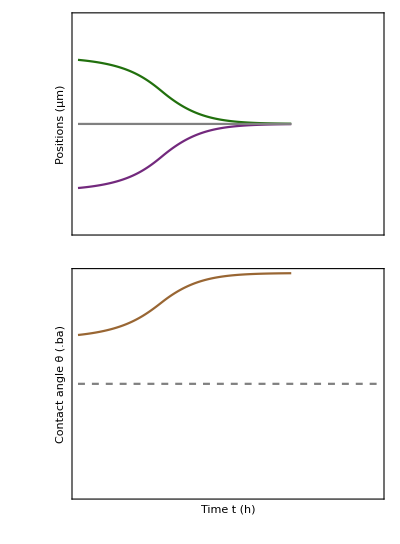

```mathematica
(* PLOTS ONLY POSITIONS AND ANGLE *)
valratio = 0.7;
dynplots = GraphicsColumn[{

ListPlot[{Transpose[{time,xrightev}],Transpose[{time,xleftev}],Transpose[{time,x0ev}]},
Joined->True,
PlotStyle->{RGBColor[0.13,0.44,0.05],RGBColor[0.45,0.16,0.49],{Gray}},
PlotRange->{{0,500},{-50,50}},
Frame->True, 
FrameLabel->{None,Style["Positions (µm)",18]},  
FrameTicks->{{ticks[20], None}, {ticks[100], None}}, 
FrameTicksStyle->Directive[18], 
FrameStyle->Black,
Axes->True, 
AxesStyle->{{Gray, Dashed}, Black},
BaseStyle->{FontFamily->"Calibri"}, 
AspectRatio->valratio],  

ListPlot[{Transpose[{time,θev*180/π}],{{0,90},{500,90}}},
Joined->True,
PlotStyle->{Brown,{Gray,Dashed}},
PlotRange->{{0,500},{0,180}},
Frame->True, 
FrameLabel->{Style["Time t (h)",18], Style["Contact angle θ (.ba)",18]},
FrameTicks->{{ticks[45], None}, {ticks[100], None}}, 
FrameTicksStyle->Directive[18], 
FrameStyle->Black,
Axes->True, 
AxesStyle->{{Gray, Dashed}, Black},
BaseStyle->{FontFamily->"Calibri"}, 
AspectRatio->valratio]},

ImageSize->400, Spacings->-2]
```

### Dynamic evolution for clusters in gradient stiffness gels

Assuming constant volume of the clusters, we study their time evolution in a gradient of stiffness substrate.

#### Parameters and evolutions

```mathematica
(* Parameters *)
tmax = 30000*3600;
t0 = 0;
Δt = 360; 
Lci = 15;
η = 20000;  
ζ = -2; 
x0i = 100;
x0idef = 0;
h = 5;
αζ = 1;
αζi = 1;
αP = 1;
(* Linear *) 
ζi0def = 0.00068;
ζigrad = 0.00005; (* if monostiffness, set x0i=0 *)
ξ0def = 0.22;
ξgrad = 0.0001;
P0def = 0.0042; (* choose eitherr P or γ profile *)
Pgrad = 0.0006; 
γ0def = 0.05;
γgrad = 0.03; 
(* Saturated *) 
a = 0.3; 
Estar = 140;
a2 = 0.5;     
Estar2 = 140; 
aP = 0.6;
EstarP = 10;
(* Cluster's shape *) 
L0i = 3;
Vconst = (92500 π)/3; 
Emax = 60; 
L0max = (3/2*Vconst/π)^(1/3);(* Radius to have θ=90.ba for the volume Vconst *)
Print["L0max = ", N[L0max], " µm"];

(* New shape: change of L0i and thus Hi to keep the same volume  *) 
Clear[Hi];
Hi = Solve[VolumeCluster[L0i,Hi]==Vconst, Hi, Reals][[1,1]][[2]];
R = (Hi^2+L0i^2)/(2*Hi);
Print["L0i = ", N[L0i], ", Hi = ", N[Hi], ", R = ", N[
R], ", V = ", N[Vconst], ", θ = ", N[180-ArcSin[L0i/R]*180/π], " ζ = ", N[ζ], " Pgrad = ", N[Pgrad], " P0 = ", N[P0def]];
```

L0max = 35.8953 µm

L0i = 3., Hi = 56.8222, R = 28.4903, V = 96865.8, θ = 173.956 ζ = -2. Pgrad = 0.0006 P0 = 0.0042

```mathematica
(* Evolution: choose *) 
evolutionVOLUMEsaturated[t0,tmax,Δt,Emax,x0i,x0idef,L0i,Lci,E0,Egrad,Estar,a,ζ*αζ,η,ξ0def,Estar2,a2,P0def,Pgrad,Hi,h,αζi,αP];              (* saturated traction and friction, and linear pressure, choosing P profile *)
(* evolutionVOLUMEsaturatedγ[t0,tmax,Δt,Emax,x0i,x0idef,L0i,Lci,E0,Egrad,Estar,a,ζ,η,ξ0def,Estar2,a2,γ0def,γgrad,Hi,h,αζi,αP];  *)       (* choosing γ profile: for volumes comparison*)
(* evolutionVOLUMEsaturatedAll[t0,tmax,Δt,Emax,x0i,x0idef,L0i,Lci,E0,Egrad,Estar,a,ζ*αζ,η,ξ0def,Estar2,a2,aP,EstarP,Hi,h,αζi,αP]; *)       (* saturated traction,friction and pressure*)
(* evolutionVOLUMElinear[3,t0,tmax,Δt,x0i,x0idef,L0i,Lci,ζi0def,ζigrad,ζ,η,ξ0def,ξgrad,P0def,Pgrad,Hi,h];  *)                             (* linear traction,friction and pressure *)
(* evolutionVOLUMElinearConstγ[3,t0,tmax,Δt,x0i,x0idef,L0i,Lci,ζi0def,ζigrad,ζ,η,ξ0def,ξgrad,Hi,γ0def,h];  *)                        (* linear traction,friction and surface tension *)
```

Cluster's volume = 96865.8µm^3

Starting with L0i = 3 the size increases when it reaches L0 = 1.99897µm at time 40.9h, position x0 = 129.708µm (traction 0.00994875kPa/µm and stiffness 4.802 kPa)

t = 50 h, E = 4.99089 kPa and L0 = 2.01635µm

t = 100 h, E = 6.11301 kPa and L0 = 2.39956µm

t = 150 h, E = 7.43936 kPa and L0 = 2.95796µm

t = 200 h, E = 9.0115 kPa and L0 = 3.63959µm

t = 250 h, E = 10.8587 kPa and L0 = 4.46389µm

t = 300 h, E = 13.0277 kPa and L0 = 5.76568µm

t = 350 h, E = 16.4379 kPa and L0 = 13.2361µm

t = 400 h, E = 24.573 kPa and L0 = 35.7749µm

At time 402.1 hours, and position x0 = 738.189µm, it goes from dewet to WET and V .10= 96865.8µm^3

t = 450 h, E = 33.2362 kPa and L0 = 37.025µm

t = 500 h, E = 40.7484 kPa and L0 = 37.4677µm

t = 550 h, E = 47.4132 kPa and L0 = 37.6867µm

t = 600 h, E = 53.4324 kPa and L0 = 37.8082µm

t = 650 h, E = 58.9421 kPa and L0 = 37.8795µm

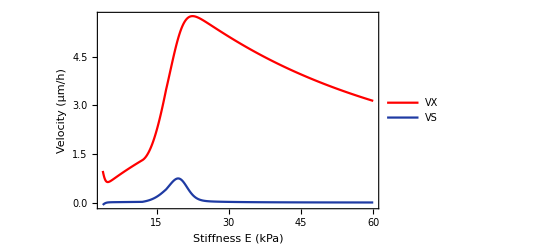

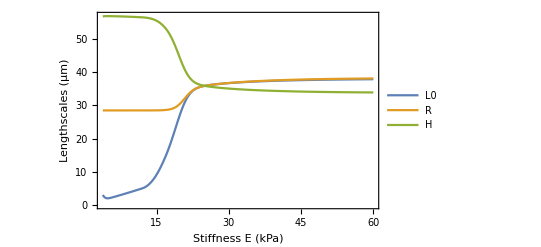

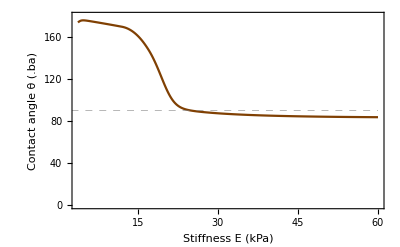

```mathematica
(* Plots *) 
a = x0ev[[1]];
b = x0ev[[-1]];     
c = Max[Max[L0ev],Max[Hev]];

ListPlot[{Transpose[{Esubstrate[x0ev[[1;;-2]],x0idef,E0,Egrad],vx0ev*3600}], Transpose[{Esubstrate[x0ev[[1;;-2]],x0idef,E0,Egrad],vL0ev*3600}]}, 
Joined->True,
PlotStyle->{Red,RGBColor[0.12,0.23,0.64],{Gray,Dashed,Thickness->0.001},{Gray,Dashed,Thickness->0.001},{Gray,Dashed,Thickness->0.001},{Gray,Dashed,Thickness->0.001}},
PlotRange->{{Esubstrate[a,x0idef,E0,Egrad], Esubstrate[b,x0idef,E0,Egrad]},All},
Frame->True, 
PlotLegends->{"VX","VS"},
FrameLabel->{Style["Stiffness E (kPa)",18],Style["Velocity (µm/h)",18]},  
FrameTicksStyle->Directive[18], 
FrameStyle->Black,
Axes->True, 
AxesStyle->{{Gray, Dashed}, Black},
BaseStyle->{FontFamily->"Calibri"}]
	
ListPlot[{Transpose[{Esubstrate[x0ev,x0idef,E0,Egrad],L0ev}],Transpose[{Esubstrate[x0ev,x0idef,E0,Egrad],Rev}],Transpose[{Esubstrate[x0ev,x0idef,E0,Egrad],Hev}]},
Joined->True,
PlotStyle->{Automatic,Automatic,Automatic,{Gray,Dashed,Thickness->0.001}},
PlotRange->{{Esubstrate[a,x0idef,E0,Egrad], Esubstrate[b,x0idef,E0,Egrad]},{0,Automatic}},
Frame->True, 
PlotLegends->{"L0","R","H"},
FrameLabel->{Style["Stiffness E (kPa)",18], Style["Lengthscales (µm)",18]},
FrameTicksStyle->Directive[18], 
FrameStyle->Black,
Axes->True, 
AxesStyle->{{Gray, Dashed}, Black},
BaseStyle->{FontFamily->"Calibri"}]
	
ListPlot[{Transpose[{Esubstrate[x0ev,x0idef,E0,Egrad],θev*180/π}],{{0,90},{Esubstrate[b,x0idef,E0,Egrad],90}}},
Joined->True,
PlotStyle->{RGBColor[0.5,0.25,0.01],{Gray,Dashed,Thickness->0.001},{Gray,Dashed,Thickness->0.001}},
PlotRange->{{Esubstrate[a,x0idef,E0,Egrad], Esubstrate[b,x0idef,E0,Egrad]},{0,180}},
Frame->True, 
FrameLabel->{Style["Stiffness E (kPa)",18], Style["Contact angle θ (.ba)",18]},
FrameTicksStyle->Directive[18], 
FrameStyle->Black,
Axes->True, 
AxesStyle->{{Gray, Dashed}, Black},
BaseStyle->{FontFamily->"Calibri"}]
```

```mathematica
(* Export and save the data *) 
m = Transpose[{time[[1;;-2]],xrightev[[1;;-2]],xleftev[[1;;-2]],x0ev[[1;;-2]],L0ev[[1;;-2]],Rev[[1;;-2]],Hev[[1;;-2]],vrightev,vleftev,vx0ev,vL0ev}];
Export["sim1.xlsx",m]; 

(* Impoprt the data from file instead of running the simulation *) 
(* namefile = "sim1";
m = Import[namefile<>ToString[".xlsx"]]; 
time = m[[1]][[All,1]];
xrightev = m[[1]][[All,2]];
xleftev = m[[1]][[All,3]];
x0ev = m[[1]][[All,4]];
L0ev = m[[1]][[All,5]];
Rev = m[[1]][[All,6]];
Hev = m[[1]][[All,7]];
vrightev = m[[1]][[All,8]];
vleftev = m[[1]][[All,9]];
vx0ev = m[[1]][[All,10]];
vL0ev = m[[1]][[All,11]]; *)
```

Times (h):  0.  199.9   349.9   399.9   449.9   499.9  599.9

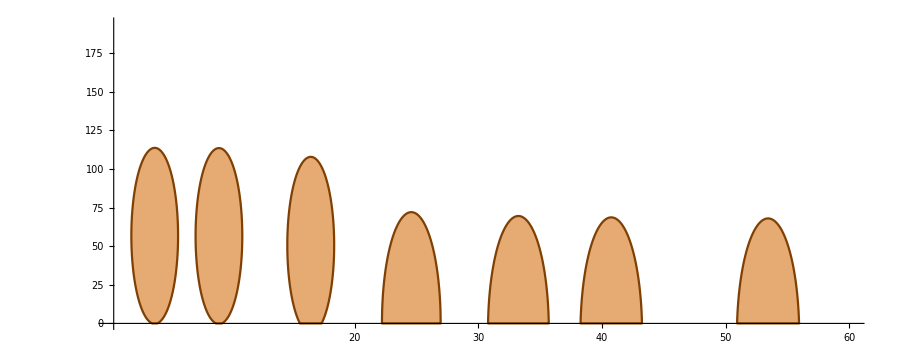

```mathematica
(* Snapchots *) 
a = x0ev[[1]]-100;
α = 2;
ind1 = 1;
ind2 = 2000;
ind3 = 3500;
ind4 = 4000;
ind5 = 4500;
ind6 = 5000;
ind7 = 6000;
Print["Times (h):  ", N[time[[ind1]]], "  ", N[time[[ind2]]], "   ",  N[time[[ind3]]], "   ", N[time[[ind4]]], "   ", N[time[[ind5]]], "   ", N[time[[ind6]]], "  ",  N[time[[ind7]]]];

Show[{
RegionPlot[(x-x0ev[[ind1]])^2+(z-α*(Hev[[ind1]]-Rev[[ind1]]))^2 ≤ α^2*Rev[[ind1]]^2,{x,x0ev[[ind1]]-α*Rev[[ind1]],x0ev[[ind1]]+α*Rev[[ind1]]},{z,0,α*Hev[[ind1]]}, 
PlotRange->{{a,b},{0,α*(c+40)}},BoundaryStyle->RGBColor[0.5,0.25,0.01],PlotStyle->RGBColor[0.9,0.67,0.45]],
RegionPlot[(x-x0ev[[ind2]])^2+(z-α*(Hev[[ind2]]-Rev[[ind2]]))^2 ≤ α^2*Rev[[ind2]]^2,{x,x0ev[[ind2]]-α*Rev[[ind2]],x0ev[[ind2]]+α*Rev[[ind2]]},{z,0,α*Hev[[ind2]]},
BoundaryStyle->RGBColor[0.5,0.25,0.01],PlotStyle->RGBColor[0.9,0.67,0.45]], 
RegionPlot[(x-x0ev[[ind3]])^2+(z-α*(Hev[[ind3]]-Rev[[ind3]]))^2 ≤ α^2*Rev[[ind3]]^2,{x,x0ev[[ind3]]-α*Rev[[ind3]],x0ev[[ind3]]+α*Rev[[ind3]]},{z,0,α*Hev[[ind3]]},
BoundaryStyle->RGBColor[0.5,0.25,0.01],PlotStyle->RGBColor[0.9,0.67,0.45]],
RegionPlot[(x-x0ev[[ind4]])^2+(z-α*(Hev[[ind4]]-Rev[[ind4]]))^2 ≤ α^2*Rev[[ind4]]^2,{x,x0ev[[ind4]]-α*Rev[[ind4]],x0ev[[ind4]]+α*Rev[[ind4]]},{z,0,α*Hev[[ind4]]},
BoundaryStyle->RGBColor[0.5,0.25,0.01],PlotStyle->RGBColor[0.9,0.67,0.45]],
RegionPlot[(x-x0ev[[ind5]])^2+(z-α*(Hev[[ind5]]-Rev[[ind5]]))^2 ≤ α^2*Rev[[ind5]]^2,{x,x0ev[[ind5]]-α*Rev[[ind5]],x0ev[[ind5]]+α*Rev[[ind5]]},{z,0,α*Hev[[ind5]]},
BoundaryStyle->RGBColor[0.5,0.25,0.01],PlotStyle->RGBColor[0.9,0.67,0.45]],
RegionPlot[(x-x0ev[[ind6]])^2+(z-α*(Hev[[ind6]]-Rev[[ind6]]))^2 ≤ α^2*Rev[[ind6]]^2,{x,x0ev[[ind6]]-α*Rev[[ind6]],x0ev[[ind6]]+α*Rev[[ind6]]},{z,0,α*Hev[[ind6]]},
BoundaryStyle->RGBColor[0.5,0.25,0.01],PlotStyle->RGBColor[0.9,0.67,0.45]],
RegionPlot[(x-x0ev[[ind7]])^2+(z-α*(Hev[[ind7]]-Rev[[ind7]]))^2 ≤ α^2*Rev[[ind7]]^2,{x,x0ev[[ind7]]-α*Rev[[ind7]],x0ev[[ind7]]+α*Rev[[ind7]]},{z,0,α*Hev[[ind7]]},
BoundaryStyle->RGBColor[0.5,0.25,0.01],PlotStyle->RGBColor[0.9,0.67,0.45]]},
Axes->{True,False},
Frame->False,
AxesStyle->Black,
MeshStyle->None,
AspectRatio->{(a-b)/c,1},
TicksStyle->Directive[Black,14], 
Ticks->{{{(20-E0)/Egrad+x0idef,"20"},{(25-E0)/Egrad+x0idef,"25"},{(30-E0)/Egrad+x0idef,"30"},{(35-E0)/Egrad+x0idef,"35"},{(40-E0)/Egrad+x0idef,"40"},{(45-E0)/Egrad+x0idef,"45"},{(50-E0)/Egrad+x0idef,"50"},{(55-E0)/Egrad+x0idef,"55"},{(60-E0)/Egrad+x0idef,"60"},
{(65-E0)/Egrad+x0idef,"65"},{(70-E0)/Egrad+x0idef,"70"},{(75-E0)/Egrad+x0idef,"75"},{(80-E0)/Egrad+x0idef,"80"},{(85-E0)/Egrad+x0idef,"85"},{(90-E0)/Egrad+x0idef,"90"},{(95-E0)/Egrad+x0idef,"95"},{(100-E0)/Egrad+x0idef,"100"}},{}},
BaseStyle->{FontFamily->"Calibri"}, 
AxesOrigin->{a,0},
ImageSize->900]
```